```mathematica
Quit[]
```

DeleteDirectory::dirne: Directory /Users/cesarecarlomella/Library/Wolfram/ApplicationData/CCompilerDriver/BuildFolder/Cesare-46097 not empty.

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Documents/GitHub/2026-higherorders-4-point-1-mass-3-loop/H

```mathematica
GetEnvironment["PATH"][[2]]
SetEnvironment["PATH"->GetEnvironment["PATH"][[2]]<>":/usr/local/bin"]
<<PolyLogTools`
$HPLAutoConvertToKnownFunctions = True
```

/usr/bin:/bin:/usr/sbin:/sbin

(****** PolyLogTools 1.3 ******)

Authors: Claude Duhr, Falko Dulat

Emails: claude.duhr@cern.ch, dulatf@slac.stanford.edu

PolyLogTools uses the implementation of the PSLQ algorithm by P. Bertok (http://library.wolfram.com/infocenter/MathSource/4263/)

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

GraphJoin::shdw: Symbol GraphJoin appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphProduct::shdw: Symbol GraphProduct appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

GraphSum::shdw: Symbol GraphSum appears in multiple contexts {Combinatorica`,System`}; definitions in context Combinatorica` may shadow or be shadowed by other definitions.

SetDelayed::write: Tag EdgeChromaticNumber in EdgeChromaticNumber[g_Graph] is Protected.

SetDelayed::write: Tag TreeQ in TreeQ[g_Graph] is Protected.

a::shdw: Symbol a appears in multiple contexts {PolyLogTools`,Global`}; definitions in context PolyLogTools` may shadow or be shadowed by other definitions.

i::shdw: Symbol i appears in multiple contexts {PolyLogTools`,Global`}; definitions in context PolyLogTools` may shadow or be shadowed by other definitions.

a$::shdw: Symbol a$ appears in multiple contexts {PolyLogTools`,Global`}; definitions in context PolyLogTools` may shadow or be shadowed by other definitions.

tmp::shdw: Symbol tmp appears in multiple contexts {PolyLogTools`,Global`}; definitions in context PolyLogTools` may shadow or be shadowed by other definitions.

tmp$::shdw: Symbol tmp$ appears in multiple contexts {PolyLogTools`,Global`}; definitions in context PolyLogTools` may shadow or be shadowed by other definitions.

i$::shdw: Symbol i$ appears in multiple contexts {PolyLogTools`,Global`}; definitions in context PolyLogTools` may shadow or be shadowed by other definitions.

True

```mathematica
Sectorbin[int_]:=Module[{},HeavisideTheta[(int[[2;;]]/. INT->List)-Table[1/2,{i,1,Length[int[[2;;]]]}]]]
computeT[int_]:=Module[{tmp},tmp=Sectorbin[int];
Total[tmp]]
computeRank[int_]:=(int/. INT->List)[[2;;]]/. a_/;a>0->0//Total
SectorID[int_]:=Module[{tmp},tmp=Sectorbin[int];
Sum[2^(i-1)*tmp[[i]],{i,1,Length[tmp]}]]
```

## Family

```mathematica
fam = "H";
SetAttributes[s, Orderless]
p={s[1,2],s[1,3],s[2,3]}
x[12]= {1-> 2, 2->1};
x[13] = {1-> 3, 3->1};
x[23]= {2-> 3,3->2};
x[123]={1-> 2, 2->3,3->1};
x[132]={1->3,3->2,2->1};
identification={p -> x,(p/. x[12]) ->  x12,(p /. x[13])->x13, (p/.x[23]) -> x23,(p /.x[123]) -> x123,(p /.x[132]) -> x132}
```

{s[1,2],s[1,3],s[2,3]}

{{s[1,2],s[1,3],s[2,3]}→x,{s[1,2],s[2,3],s[1,3]}→x12,{s[2,3],s[1,3],s[1,2]}→x13,{s[1,3],s[1,2],s[2,3]}→x23,{s[2,3],s[1,2],s[1,3]}→x123,{s[1,3],s[2,3],s[1,2]}→x132}

```mathematica
CoefficientToKira[VarCoefficient_,VarWeight_]:=Module[
{KiraFileLine},

If[VarCoefficient===0,Return[""]];

KiraFileLine=ToString[VarWeight]<>"*("<>ToString[VarCoefficient,InputForm]<>")\n";
Return[StringDelete[KiraFileLine," "]];
]

CanonicalForKira[ToTransform_]:=Module[
{KiraWeights,WeightCoef,LinearKiraWeightQ,NoWeightLessTermQ,KiraRelation},

KiraWeights=Union[Cases[ToTransform,I2[a___],{0,Infinity}],Cases[ToTransform,I2x12[a___],{0,Infinity}],Cases[ToTransform,I2x13[a___],{0,Infinity}],Cases[ToTransform,I2x23[a___],{0,Infinity}],Cases[ToTransform,I2x123[a___],{0,Infinity}],Cases[ToTransform,I2x132[a___],{0,Infinity}]];
(*extract all the coefficient*)
WeightCoef=CoefficientArrays[ToTransform,KiraWeights]//Normal;

(*Consistency check:
verify that is linear   *)
LinearKiraWeightQ=Length[WeightCoef]===2;
If[Not[LinearKiraWeightQ],Print["Error: Equation is not linear. Check input."]; Abort[]];
NoWeightLessTermQ=WeightCoef[[1]]==0;
If[Not[NoWeightLessTermQ],Print["Error: Constant term is not 0. Check input."]; Abort[]];


(*Remove 0 coefficients*)
WeightCoef=WeightCoef[[2]];

(*Convert to Kira string: *)
KiraRelation=StringJoin@MapThread[CoefficientToKira,{WeightCoef,KiraWeights}];
Return[KiraRelation]
]
```

### Shift basis to PL when possible

```mathematica
(*CountEntries[int_]:= Module[{},Return[Total[((int/.INT->List)[[2;;]] ) /. {-1->1, -2->2,-3->3}]]];*)
```

```mathematica
basis=((4-d)/2)^6 Import["./deq-H/bdef.m"] /. INT["H",a__,{b__}]-> INT[H,b] /. {t -> y, u  -> 1-x-y};
Propagators = {(k1+p2)^2,(k2-p2)^2,(k2)^2,(k1+k2+k3)^2,(k1+k2+k3+p1)^2,(k3+p1)^2,(k3+p1+p3)^2,(k1-p1-p3)^2,(k1+k3)^2,(k1+k2)^2,(k1)^2,(k3)^2,(k1-p1)^2,(k2-p3)^2,(k3-p2)^2};
```

```mathematica
(*Propagators//TableForm*)
```

```mathematica
basis // TableForm;
```

```mathematica
ints = Union@Cases[basis, _INT, ∞];
```

```mathematica
deq=Import["./deq-H/deq-full.m"];
```

```mathematica
mis=Table[mi[i], {i,1,371}];
```

```mathematica
Import["./deq-H/bdef.m"][[156;;157]]
```

{INT[H,8,987,8,0,{1,1,0,1,1,0,1,1,1,1,0,0,0,0,0}],INT[H,8,255,8,0,{1,1,1,1,1,1,1,1,0,0,0,0,0,0,0}]}

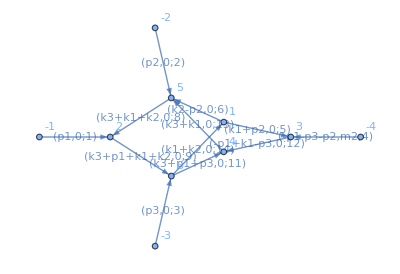

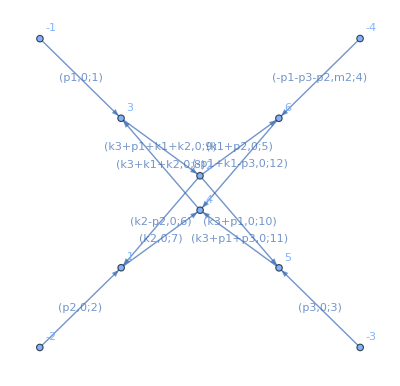

```mathematica
Import["./H/all/H_08_00987.dot"]
Import["./H/all/H_08_00255.dot"]
```

```mathematica
dy=(CoefficientArrays[Table[dmidt[i], {i,1,371}] /. deq,mis][[2]]//Normal) /. {t  ->  y, u -> (1-x-y)};
du=(CoefficientArrays[Table[dmidu[i], {i,1,371}] /. deq,mis][[2]]//Normal) /. {t  ->  y, u -> (1-x-y)};
dx=- du;
dy = -du+dy ;
```

```mathematica
dx[[156,156]]/.ep -> 0//Simplify
dx[[157,157]]/.ep -> 0//Simplify
```

-(-1+2 x+y)/(2 x (-1+x+y))

-(-1+2 x+y)/(2 x (-1+x+y))

```mathematica
R = IdentityMatrix[371];
R[[156,156]] = sqrt;
R[[157,157]] = sqrt;
```

```mathematica
mat1=(D[R /. sqrt -> sqrt[x,y] ,x] /.Derivative[1,0][sqrt][x,y]-> 1/2 sqrt/(x y (1-x-y))D[x y (1-x-y),x]).(Inverse[R] /. 1/sqrt -> (sqrt)/x/y/(1-x-y)) /. (sqrt^2 -> x y (1-x-y));
tmp=R.dx.(Inverse[R] /. 1/sqrt -> (sqrt)/x/y/(1-x-y)) /. sqrt^2 ->  x y (1-x-y) ;
dxepsFactorised = tmp + mat1;
```

```mathematica
mat2=(D[R /. sqrt -> sqrt[x,y] ,y] /.Derivative[0,1][sqrt][x,y]-> 1/2 sqrt/(x y (1-x-y))D[x y (1-x-y),y]).(Inverse[R] /. 1/sqrt -> (sqrt)/x/y/(1-x-y)) /. (sqrt^2 -> x y (1-x-y));
tmp=R.dy.(Inverse[R] /. 1/sqrt -> (sqrt)/x/y/(1-x-y)) /. sqrt^2 ->  x y (1-x-y);
dyepsFactorised = tmp + mat2;
```

```mathematica
dy[[156,156]]//Simplify
dy[[157,157]]//Simplify
```

(x-(1+4 ep) x^2-4 ep x (-1+y)-3 x y+(1-4 ep-2 y) y)/(2 y (-1+x+y) (x+y))

-(-1+x+2 y)/(2 y (-1+x+y))

```mathematica
mat1[[156,156]]
mat1[[157,157]]
```

(-x y+(1-x-y) y)/(2 x (1-x-y) y)

(-x y+(1-x-y) y)/(2 x (1-x-y) y)

```mathematica
dxepsFactorised[[156,156]]//Simplify
dyepsFactorised[[157,157]]//Simplify
```

-(2 ep ((-1+y) y+x (1+y)))/(x (-1+x+y) (x+y))

0

```mathematica
dxepsFactorised /. ep -> 0//Flatten //Union // Simplify
dyepsFactorised /. ep -> 0//Flatten //Union // Simplify
```

{0,0,0}

{0,0,0}

```mathematica
(*Export["./tmp/dxepsFactorised.m",dxepsFactorised]
Export["./tmp/dyepsFactorised.m",dyepsFactorised]*)
```

```mathematica
(*Union@Cases[Import["../../Subleading_Color_input/I1/Atilde.m"], _Log,∞]/.m2-> 1 /. {s-> x, t -> y}
Union@Cases[Import["../../Subleading_Color_input/D/input/Atilde.m"], _Log,∞]/.m2-> 1 /. {s-> x, t -> y}
Union@Cases[Import["../../Subleading_Color_input/G2/input/Atilde.m"], _Log,∞]/.m2-> 1 /. {s-> x, t -> y}
Join[%,%%, %%%] // Union*)
```

```mathematica
letters={Log[-1+x],Log[x],Log[-1+y],Log[y],Log[-(1-x)^2+y],Log[-1+x+y],Log[x+y],Log[-x+x^2+y],Log[x^2+y+x y],Log[-1+(1+x) y],Log[1+(-2+x) y+y^2],Log[1+x^2+x (-2+y)],Log[1-x-2 y+y^2],Log[x-y+y^2],Log[1-x-x y]};
```

```mathematica
sqroot= {Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))],Log[(x y- I √(x (1-x-y) y))/(x y+ I √(x (1-x-y) y))]}
DSrules={Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))]->(sqrt ⅈ y (-1+2 x+y))/(x y (1-x-y) (-1+x) (x+y)),Log[(x y-I √(x (1-x-y) y))/(x y+I √(x (1-x-y) y))]->(sqrt ⅈ y)/(x y (1-x-y)(1- x))};
DTrules ={Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))]->-(ⅈ x sqrt)/(x y (1-x-y) (x+y)),Log[(x y-I √(x (1-x-y) y))/(x y+I √(x (1-x-y) y))] ->(ⅈ x sqrt)/((1- y)x y (1-x-y))};
```

{Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))],Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]}

```mathematica
(*dxepsFactorised[[156]]=(dxepsFactorised[[156]]//Simplify);
dxepsFactorised[[157]]=(dxepsFactorised[[157]]//Simplify);
dyepsFactorised[[156]]=(dyepsFactorised[[156]]//Simplify);
dyepsFactorised[[157]]=(dyepsFactorised[[157]]//Simplify);
dxepsFactorised = dxepsFactorised/.ep -> 1;
dyepsFactorised = dyepsFactorised/.ep -> 1;
*)
```

```mathematica
(*derLx=Thread[Rule[{l[1],l[2],l[3],l[4],l[5],l[6],l[7],l[8],l[9],l[10], l[11],l[12], l[13], l[14],l[15]},D[letters,x]]];
derLy=Thread[Rule[{l[1],l[2],l[3],l[4],l[5],l[6],l[7],l[8],l[9],l[10],l[11],l[12],l[13],l[14],l[15]},D[letters,y]]];
derLxroot =  {l[19]->(sqrt ⅈ y (-1+2 x+y))/(x y (1-x-y) (-1+x) (x+y)),l[20]->(sqrt ⅈ y)/(x y (1-x-y)(1- x))};
derLyroot =  {l[19]->-(ⅈ x sqrt)/(x y (1-x-y) (x+y)),l[20]->(ⅈ x sqrt)/((1- y)x y (1-x-y))};*)
```

```mathematica
(*matrS = dxepsFactorised;
matrT = dyepsFactorised;*)
```

```mathematica
(*ansatz = Import["./tmpansatz.m"];*)
```

```mathematica
(*ansatz = Table[Sum[a[i,j][k]l[k], {k,1,}], {i,1,371}, {j,1,371}];*)
```

```mathematica
(*counter = 0;
Do[
tmp=Collect[Numerator[Together[(ansatz[[i,j]]/.derLx /. derLxroot)-matrS[[i,j]]]], {x,y,sqrt}, FF];
eqs =Union@Cases[tmp, _FF,∞] /. FF[a__]:> Thread[Equal[a,0]];
tmp=Collect[Numerator[Together[(ansatz[[i,j]]/.derLy /. derLyroot)-matrT[[i,j]]]], {x,y,sqrt}, FF];
eqs =Join[eqs,Union@Cases[tmp, _FF,∞] /. FF[a__]:> Thread[Equal[a,0]]];
sol = Flatten[Solve[eqs]];
ansatz[[i,j]] = ansatz[[i,j]] /. sol;
counter = counter +1;If[Mod[counter,100]===0,Print[i,"  ,   ", j]], {i,1,371}, {j,1,371}]*)
```

```mathematica
(**)
```

```mathematica
(*map=Thread[Rule[{l[1],l[2],l[3],l[4],l[5],l[6],l[7],l[8],l[9],l[10], l[11],l[12], l[13], l[14],l[15]}, letters]];*)
```

```mathematica
(*ansatz=ansatz /. map /. {l[19]->Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))],l[20]-> Log[(x y- I √(x (1-x-y) y))/(x y+ I √(x (1-x-y) y))]};*)
```

```mathematica
Basis = Import["./input/basis.m"];
Atilde = Import["./input/Atilde.m"];
```

```mathematica
(*D[Atilde[[]],x] - dxepsFactorised /. ep -> 1 /. sqrt -> Sqrt[x y (1-x-y)]// Together// Flatten //Union
D[Atilde[[]],y] - dyepsFactorised /. ep -> 1 /. sqrt -> Sqrt[x y (1-x-y)]// Together// Flatten //Union*)
```

```mathematica
Clear[H]
```

```mathematica
(*Collect integrals to shift*)
integrals=Union[Cases[Basis, _INT, Infinity]];
integrals=integrals/. INT[a_,b__] -> a[b];
Export["toshift/int.txt", integrals]
```

toshift/int.txt

```mathematica
Shifts=Import["./toshift/list.m"];
Shifts=Extract[Shifts,Position[Shifts[[;;,1]], INT[fam, a__]]];
Shifts=Extract[Shifts,Union[Join[Position[Shifts[[;;,2]], INT["PL",a__]],Position[Shifts[[;;,2]], INT["PLx13",a__]],Position[Shifts[[;;,2]], INT["PLx12",a__]],Position[Shifts[[;;,2]], INT["PLx23",a__]],Position[Shifts[[;;,2]], INT["PLx132",a__]],Position[Shifts[[;;,2]], INT["PLx123",a__]]]  /. {a_, b_, c_}-> {a} /.  {a_, b_}-> {a} ]];
Join[Position[Shifts[[;;,2]], INT[fam, a__]]/. {a_, b_, c_}-> {a} /.  {a_, b_}-> {a}//Union,Position[Shifts[[;;,2]], INT[fam<>"x12", a__]]/. {a_, b_, c_}-> {a} /.  {a_, b_}-> {a}//Union,Position[Shifts[[;;,2]], INT[fam<>"x13", a__]]/. {a_, b_, c_}-> {a} /.  {a_, b_}-> {a}//Union,Position[Shifts[[;;,2]], INT[fam<>"x23", a__]]/. {a_, b_, c_}-> {a} /.  {a_, b_}-> {a}//Union,Position[Shifts[[;;,2]], INT[fam<>"x123", a__]]/. {a_, b_, c_}-> {a} /.  {a_, b_}-> {a}//Union,Position[Shifts[[;;,2]], INT[fam<>"x132", a__]]/. {a_, b_, c_}-> {a} /.  {a_, b_}-> {a}//Union];
```

```mathematica
Shifts=Extract[Shifts,Complement[Table[{i},{i,1,Length[Shifts]}], %]];
Shifts = Shifts /. INT[a_,t__,{b__}]:> INT[ToExpression[a],b];
shiftedBasis = Basis /. Shifts;
shiftedBasis = shiftedBasis /. s-> x /. t-> y /. s13 -> y /. s23 -> 1-x-y /. m2 -> 1;
toExpressAsPL=Union[Cases[shiftedBasis  /. INT[ToExpression[fam],a__] -> 0, _INT, Infinity]];
(*uncross*)
Export["./toshift/PLtoBASISLC.txt", Union[toExpressAsPL  /. PLx13 -> PL /. PLx123 -> PL/.PLx12-> PL /.PLx23 -> PL /.PLx132 -> PL/. INT[a_,b__] -> a[b]]]
Export["./toshift/PLtoBASISLC.m", Union[toExpressAsPL  /. PLx13 -> PL /. PLx123 -> PL/.PLx12-> PL /.PLx23 -> PL /.PLx132 -> PL/. INT[a_,b__] -> a[b]]]
```

Complement::normal: Nonatomic expression expected at position 2 in Complement[{},toshift/int.txt].

Extract::psl1: Position specification Complement[{},toshift/int.txt] in Extract[Shifts,Complement[{},toshift/int.txt]] is not applicable.

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

ReplaceAll::reps: {TerminatedEvaluation[RecursionLimit]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

./toshift/PLtoBASISLC.txt

./toshift/PLtoBASISLC.m

```mathematica
(*Export["../toPL_BASISLC.txt",(part1 /. PL[a__]-> INT[PL,a]/. shiftstoBASISLC["x"] /. _BASISLC -> 0 // Union )[[2;;]] /. INT[PL,a___]-> PL[a]]*)
```

```mathematica
(*Complement[Union[toExpressAsPL /.PLx13 -> PL /. PLx123 -> PL/.PLx12-> PL /.PLx23 -> PL /.PLx132 -> PL],shiftstoBASISLC["x"][[;;,1]]];*)
```

```mathematica
shiftstoBASISLC["x"]=Import["../kira_inputPLtoBASISLC_5.txt.m"] /. s23 -> 1-y-x /. s13 -> y /. PL[a__] -> INT[PL,a] ;
shiftstoBASISLC["x"]=Join[shiftstoBASISLC["x"],Import["./kira_inputextra.txt.m"]] /. s23 -> 1-y-x /. s13 -> y /. PL[a__] -> INT[PL,a] ;
(*cross reduction*)
shiftstoBASISLC["x12"]=shiftstoBASISLC["x"]  /. BASISLC -> BASISLCx12 /. PL-> PLx12 /. y-> 1-x-y;
shiftstoBASISLC["x13"]=shiftstoBASISLC["x"]  /. BASISLC -> BASISLCx13 /. PL-> PLx13 /. x -> 1-x-y;
shiftstoBASISLC["x23"]=shiftstoBASISLC["x"]  /. BASISLC -> BASISLCx23 /. PL-> PLx23 /.{ x ->y, y-> x};
shiftstoBASISLC["x123"]=shiftstoBASISLC["x"]  /. BASISLC -> BASISLCx123 /. PL-> PLx123 /.{ x -> 1-x-y, y-> x};
shiftstoBASISLC["x132"]=shiftstoBASISLC["x"]  /. BASISLC -> BASISLCx132 /. PL-> PLx132 /.{ x ->y, y-> 1-x-y};
```

Import::nffil: File ../kira_inputPLtoBASISLC_5.txt.m not found during Import.

```mathematica
Export["extra.txt",(Union@Cases[shiftedBasis[[]] /. _BASISLC -> 0  /. INT[H,a__]-> 0, _INT,∞] /. PLx12 -> PL /. PLx132 -> PL/.PLx123 -> PL /.PLx13 -> PL  /.PLx23 -> PL // Union) /. INT[PL,a__]-> PL[a]]
```

extra.txt

```mathematica
Do[shiftedBasis[[i]]=Collect[shiftedBasis[[i]] /. shiftstoBASISLC["x"]  /. shiftstoBASISLC["x13"]  /. shiftstoBASISLC["x12"] /. shiftstoBASISLC["x23"] /. shiftstoBASISLC["x123"]/. shiftstoBASISLC["x132"] , {_INT, _BASISLC},Together]; , {i,1,Length[shiftedBasis]}]
```

```mathematica
Print["Surviving ",shiftedBasis /. _BASISLC ->  0 /. _BASISLCx13 -> 0 /. _BASISLCx123 -> 0 /. _BASISLCx12 -> 0 /. _BASISLCx23 -> 0 /. _BASISLCx132 -> 0  //Union // Length]
Print["ShiftedBasis determined"]
Export["shiftedBasis/shiftedBasis.m",shiftedBasis]
```

Surviving 239

ShiftedBasis determined

shiftedBasis/shiftedBasis.m

```mathematica
shiftedBasis = Import["shiftedBasis/shiftedBasis.m"];
onlyplanar=Position[Map[FreeQ[#, INT[b__,a__]]&,shiftedBasis], True];
Print["onlyplanar", onlyplanar]
```

onlyplanar{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{23},{25},{26},{28},{29},{30},{31},{33},{35},{36},{37},{38},{39},{41},{42},{44},{45},{46},{47},{48},{49},{50},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{64},{65},{66},{67},{69},{70},{71},{73},{74},{76},{77},{78},{79},{80},{81},{82},{83},{85},{86},{87},{88},{89},{90},{91},{93},{95},{96},{97},{98},{99},{100},{101},{103},{106},{116},{125},{126},{128},{129},{131},{132},{134},{135},{136},{137},{138},{139},{140},{142},{143},{144},{145},{146},{147},{148},{149},{150},{152},{153},{154},{155},{158},{159},{164},{165},{193},{194},{195},{196},{197},{200},{201},{202},{205},{277},{290},{291},{310},{335}}

```mathematica
DumpGet["../../change_fibration/fibrationXY/XYfibr.mx"]
DumpGet["../../change_fibration/fibrationXY/YXfibr.mx"]
fibrDisp = Dispatch[fibrXY];
```

DumpGet::noopen: Cannot open ../../change_fibration/fibrationXY/XYfibr.mx.

DumpGet[../../change_fibration/fibrationXY/XYfibr.mx]

DumpGet::noopen: Cannot open ../../change_fibration/fibrationXY/YXfibr.mx.

DumpGet[../../change_fibration/fibrationXY/YXfibr.mx]

```mathematica
pls=Collect[(Extract[shiftedBasis,onlyplanar] ), {_BASISLC, _BASISLCx13, _BASISLCx12, _BASISLCx23, _BASISLCx123, _BASISLCx132}, Together] /. d-> 4 -2 eps /. {m2 -> 1, s-> x, t-> y, s13 -> y, s23 -> 1-x-y};
```

```mathematica
PLSolutionsMap[""]= Import["../planar_stuff/pl.m"];
Print["done"]
PLSolutionsMap["x12"]= Import["../planar_stuff/plx12.m"];
Print["done"]
PLSolutionsMap["x13"]= Import["../planar_stuff/plx13.m"];
Print["done"]
PLSolutionsMap["x23"]= Import["../planar_stuff/plx23.m"];
Print["done"]
PLSolutionsMap["x123"]= Import["../planar_stuff/plx123.m"];
Print["done"]
PLSolutionsMap["x132"]= Import["../planar_stuff/plx132.m"];
Print["done"]
```

done

done

done

«3 more identical outputs»

```mathematica
sub1=Dispatch[PLSolutionsMap[""]];
Print["done"]
sub2=Dispatch[PLSolutionsMap["x12"]];
Print["done"]
sub3=Dispatch[PLSolutionsMap["x13"]];
Print["done"]
sub4=Dispatch[PLSolutionsMap["x23"]];
Print["done"]
sub5=Dispatch[PLSolutionsMap["x123"]];
Print["done"]
sub6 = Dispatch[PLSolutionsMap["x132"]];
Print["done"]
```

done

done

done

«3 more identical outputs»

```mathematica
pls//Length
Do[pls[[i]]= Collect[Collect[pls[[i]] /.sub1 /. sub2 /. sub3 /.sub4 /.sub5 /.sub6, {eps}] /. fibrDisp//ShuffleG,   {eps, _G, _Zeta ,Pi}, Together]; Print[i], {i,1,Length[pls]}]
Do[pls[[i]] =Collect[Collect[pls[[i]], {_G, _Zeta, Pi}, Together], {eps, _G, _Zeta, Pi},Together];Print[i];, {i,1,Length[pls]}]
```

133

122

123

124

125

126

127

128

129

130

131

132

133

```mathematica
SolutionWithPlanar=shiftedBasis;
Do[SolutionWithPlanar[[onlyplanar[[i,1]]]]= pls[[i]], {i,1,Length[onlyplanar]}];
```

```mathematica
(*Export["./results/planarInsertedXY.m",SolutionWithPlanar]*)
SolutionWithPlanar= Import["./results/planarInsertedXY.m"];
```

```mathematica
onlyplanar//Length
```

133

```mathematica
SolutionWithPlanar//Length
```

371

### Load Differential equation Matrix

```mathematica
Basis = Import["./input/basis.m"];
Atilde = Import["./input/Atilde.m"];
```

```mathematica
Atilde=Atilde /. s-> x /. t-> y /. m2 -> 1;
```

```mathematica
alphabet=Cases[Atilde, _Log, Infinity] //Union;
alphabetI=alphabet /. Sqrt[-x (1-x-y)y] -> I Sqrt[ x (1 -x -y )y]
```

{Log[-1+x],Log[x],Log[-1+y],Log[y],Log[-(1-x)^2+y],Log[-1+x+y],Log[x+y],Log[-x+x^2+y],Log[1-x-x y],Log[-1+(1+x) y],Log[1-x-2 y+y^2],Log[x-y+y^2],Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))],Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]}

```mathematica
Atilde/. Sqrt[-x (1-x-y)y] -> I Sqrt[ x (1 -x -y )y]/.Thread[Rule[alphabetI,0]]//Flatten //Union
```

{0}

### Check Planar solutions

```mathematica
replacementSQRT={Log[(x (1-x-y)-√(-x (1-x-y) y))/(x (1-x-y)+√(-x (1-x-y) y))]->Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))],Log[(x y-√(-x (1-x-y) y))/(x y+√(-x (1-x-y) y))]->Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]};
DSrules={Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))]->(ⅈ y (-1+2 x+y))/(sqrt (-1+x) (x+y)),Log[(x y-I √(x (1-x-y) y))/(x y+I √(x (1-x-y) y))]->(ⅈ y)/(sqrt-sqrt x)}
DTrules ={Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))]->-(ⅈ x)/(sqrt (x+y)),Log[(x y-I √(x (1-x-y) y))/(x y+I √(x (1-x-y) y))] ->(ⅈ x)/(sqrt-sqrt y)}
Atilde=Atilde /. replacementSQRT;
Cases[Atilde , _Log, Infinity]//Union
```

{Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))]→(ⅈ y (-1+2 x+y))/(sqrt (-1+x) (x+y)),Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]→(ⅈ y)/(sqrt-sqrt x)}

{Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))]→-(ⅈ x)/(sqrt (x+y)),Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]→(ⅈ x)/(sqrt-sqrt y)}

{Log[-1+x],Log[x],Log[-1+y],Log[y],Log[-(1-x)^2+y],Log[-1+x+y],Log[x+y],Log[-x+x^2+y],Log[1-x-x y],Log[-1+(1+x) y],Log[1-x-2 y+y^2],Log[x-y+y^2],Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))],Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]}

```mathematica
sqrtpart = Coefficient[Atilde, Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))]]Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))] +  Coefficient[Atilde,Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]] Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))];
dx=D[Atilde  /. {Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))] -> 0,Log[(x y-I √(x (1-x-y) y))/(x y+I √(x (1-x-y) y))]-> 0 },x] +( sqrtpart  /. DSrules) ;
dy=D[Atilde  /. {Log[(x (1-x-y)-I √(x (1-x-y) y))/(x (1-x-y)+I √(x (1-x-y) y))] -> 0,Log[(x y-I √(x (1-x-y) y))/(x y+I √(x (1-x-y) y))]-> 0 },y] +( sqrtpart  /. DTrules);
```

```mathematica
rrs ={y/((-1+x) sqrt) -> 1/r1,y/(sqrt (x+y))->1/r2,x/((-1+y) sqrt)-> 1/r3, x/(sqrt (x+y))-> 1/r4  }
revertRRS =Thread[Rule[ rrs[[;;,2]], rrs[[;;,1]]]]
```

{y/(sqrt (-1+x))→1/r1,y/(sqrt (x+y))→1/r2,x/(sqrt (-1+y))→1/r3,x/(sqrt (x+y))→1/r4}

{1/r1→y/(sqrt (-1+x)),1/r2→y/(sqrt (x+y)),1/r3→x/(sqrt (-1+y)),1/r4→x/(sqrt (x+y))}

```mathematica
dx = Apart[dx,x] /. rrs;
dy = Apart[dy,y] /. rrs;
```

```mathematica
dx // Variables
dy// Variables
```

{r1,r2,x,y}

{r3,r4,x,y}

```mathematica
rrs
```

{y/(sqrt (-1+x))→1/r1,y/(sqrt (x+y))→1/r2,x/(sqrt (-1+y))→1/r3,x/(sqrt (x+y))→1/r4}

```mathematica
revertRRS
```

{1/r1→y/(sqrt (-1+x)),1/r2→y/(sqrt (x+y)),1/r3→x/(sqrt (-1+y)),1/r4→x/(sqrt (x+y))}

```mathematica
(*Export["./numerical_evaluation/Atilde.m", Atilde]
Export["./numerical_evaluation/dx.m", dx]
Export["./numerical_evaluation/dy.m", dy]*)
```

```mathematica
(*D[Atilde[[;;]],x]-dx[[;;]] /.revertRRS /. sqrt -> √(-x y (-1+x+y))//Simplify//Flatten //Union
D[Atilde[[;;]],y]-dy[[;;]] /.revertRRS /. sqrt -> √(-x y (-1+x+y))//Simplify//Flatten //Union*)
```

```mathematica
(*Export["./numerical_evaluation/dx.m", dx]
Export["./numerical_evaluation/dy.m", dy]*)
```

./numerical_evaluation/dx.m

./numerical_evaluation/dy.m

## SOLUTION

#### Boundary in x and y

```mathematica
alphabetI
alphabetNaming= Thread[Rule[alphabetI, Table[LL[i], {i,1,Length[alphabetI]}]]];
LLs = Table[LL[i], {i,1,Length[alphabetI]}];
```

{Log[-1+x],Log[x],Log[-1+y],Log[y],Log[-(1-x)^2+y],Log[-1+x+y],Log[x+y],Log[-x+x^2+y],Log[1-x-x y],Log[-1+(1+x) y],Log[1-x-2 y+y^2],Log[x-y+y^2],Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))],Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]}

```mathematica
alphabet
```

{Log[-1+x],Log[x],Log[-1+y],Log[y],Log[-(1-x)^2+y],Log[-1+x+y],Log[x+y],Log[-x+x^2+y],Log[1-x-x y],Log[-1+(1+x) y],Log[1-x-2 y+y^2],Log[x-y+y^2],Log[(x (1-x-y)-ⅈ √(x (1-x-y) y))/(x (1-x-y)+ⅈ √(x (1-x-y) y))],Log[(x y-ⅈ √(x (1-x-y) y))/(x y+ⅈ √(x (1-x-y) y))]}

```mathematica
arglogs = alphabetI /. Log ->Identity;
Do[Axy[i[[1]]]=Coefficient[Atilde /. alphabetNaming, i], {i,LLs}]
```

#### L1: limit x -> 0 , y fixed

```mathematica
Series[arglogs , {x,0,1}, Assumptions->{x>0, y>0, y<1}] //Normal
Position[Coefficient[%,x,0],0]//Flatten
toexp[1]=Sum[Axy[i], {i,%}];
Export["./matrix_to_JD/toexp1.m", toexp[1]]
Export["./numerical_evaluation/Ax.m", toexp[1]]
```

{-1+x,x,-1+y,y,-1+2 x+y,-1+x+y,x+y,-x+y,1+x (-1-y),-1+y+x y,1-x-2 y+y^2,x-y+y^2,-1+(2 ⅈ √x (-1+y))/(√(-((-1+y) y)))+x ((1-y)/y+(√(-y/(-1+y)))/(2 √(-((-1+y) y)))+(-2+5 y-2 y^2)/(2 (-1+y) y)),-1-(2 ⅈ √x y)/(√(-((-1+y) y)))+x (-y/(-1+y)+(√(-y/(-1+y)))/(2 √(-((-1+y) y)))+(y-2 y^2)/(2 (-1+y) y))}

{2}

./matrix_to_JD/toexp1.m

./numerical_evaluation/Ax.m

```mathematica
(*JD= Import["./matrix_to_JD/toJD/JD1.m"];
eigenvalues= Import["./matrix_to_JD/toJD/eigenvalues1.m"];
Expon[1] = Import["./matrix_to_JD/toJD/expon1.m"];
totake=((Join[Cases[eigenvalues, Power[delta,a_ eps] /; a>0, Infinity], Cases[eigenvalues, Power[delta, eps] , Infinity]]//Union) /. Power[delta,t_]-> t /. eps-> 1)
Do[matr[i]=Coefficient[Expon[1],delta^( i eps)] /. Log[delta] -> 0 , {i,totake}];
boundaryMxy[1] = matr[totake[[1]]];
If[Length[totake]>1,
Do[boundaryMxy[1] = Join[boundaryMxy[1], matr[totake[[i]]]], {i,2,Length[totake]}]]*)
```

```mathematica
(*Export["boundary_matrices/b1.m",boundaryMxy[1]]*)
```

```mathematica
(*exp1=Import["./matrix_to_JD/exponentiated1.m"];*)
```

```mathematica
boundaryMxy[1]=Import["./matrix_to_JD/toJD/P_1_toexp1.m"];
```

```mathematica
boundaryMxy[1]//MatrixRank
```

96

#### L2: limit y -> 0 , x fixed

```mathematica
Series[arglogs , {y,0,1}, Assumptions->{x>0,x<1, y>0, y<1}] //Normal
Position[Coefficient[%,y,0],0]//Flatten
toexp[2]=Sum[Axy[i], {i,%}];
Export["./matrix_to_JD/toexp2.m", toexp[2]]
```

{-1+x,x,-1+y,y,-(-1+x)^2+y,-1+x+y,x+y,-x+x^2+y,1-x-x y,-1+(1+x) y,1-x-2 y,x-y,1+(2 ⅈ √(-((-1+x) x)) √y)/((-1+x) x)+(2 y)/((-1+x) x),-1-(2 ⅈ x √y)/(√(-((-1+x) x)))+(-x/(-1+x)+(√(-x/(-1+x)))/(2 √(-((-1+x) x)))+(x-2 x^2)/(2 (-1+x) x)) y}

{4}

./matrix_to_JD/toexp2.m

```mathematica
(*JD= Import["./matrix_to_JD/toJD/JD2.m"];
eigenvalues= Import["./matrix_to_JD/toJD/eigenvalues2.m"];
Expon[2] = Import["./matrix_to_JD/toJD/expon2.m"];
totake=((Join[Cases[eigenvalues, Power[delta,a_ eps] /; a>0, Infinity], Cases[eigenvalues, Power[delta, eps] , Infinity]]//Union) /. Power[delta,t_]-> t /. eps-> 1)
Do[matr[i]=Coefficient[Expon[2],delta^( i eps)] /. Log[delta] -> 0 , {i,totake}];
boundaryMxy[2] = matr[totake[[1]]];
If[Length[totake]>1,
Do[boundaryMxy[2] = Join[boundaryMxy[2], matr[totake[[i]]]], {i,2,Length[totake]}]]
boundaryMxy[2]//Variables*)
```

```mathematica
(*Export["boundary_matrices/b2.m",boundaryMxy[2]]*)
```

```mathematica
boundaryMxy[2]=Import["./matrix_to_JD/toJD/P_1_toexp2.m"];
```

```mathematica
boundaryMxy[2]//MatrixRank
```

$Aborted

#### L3: limit x -> 0, y->0

```mathematica
param={x -> delta, y ->  delta rho} ;
Series[arglogs /.  param, {delta,0,1}, Assumptions->{delta>0, rho >0}] //Normal
Position[Coefficient[%,delta,0],0]//Flatten
toexp[3]=Sum[Axy[i], {i,%}];
Export["./matrix_to_JD/toexp3.m", toexp[3]]
```

{-1+delta,delta,-1+delta rho,delta rho,-1+delta (2+rho),-1+delta (1+rho),delta (1+rho),delta (-1+rho),1-delta,-1+delta rho,1+delta (-1-2 rho),delta (1-rho),(-ⅈ-√rho)/(-ⅈ+√rho)+(ⅈ delta (ⅈ √rho+rho))/(-ⅈ+√rho),-1-2 ⅈ delta √rho}

{2,4,7,8,12}

./matrix_to_JD/toexp3.m

```mathematica
(*JD= Import["./matrix_to_JD/toJD/JD3.m"];
eigenvalues= Import["./matrix_to_JD/toJD/eigenvalues3.m"];
Expon[3] = Import["./matrix_to_JD/toJD/expon3.m"];
totake=((Join[Cases[eigenvalues, Power[delta,a_ eps] /; a>0, Infinity], Cases[eigenvalues, Power[delta, eps] , Infinity]]//Union) /. Power[delta,t_]-> t /. eps-> 1)
Do[matr[i]=Coefficient[Expon[3],delta^( i eps)] /. Log[delta] -> 0 , {i,totake}];
boundaryMxy[3] = matr[totake[[1]]];
If[Length[totake]>1,
Do[boundaryMxy[3] = Join[boundaryMxy[3], matr[totake[[i]]]], {i,2,Length[totake]}]]
boundaryMxy[3]//Variables*)
```

{2}

{}

```mathematica
(*Export["boundary_matrices/b3.m",boundaryMxy[3]]*)
```

boundary_matrices/b3.m

```mathematica
boundaryMxy[3] =Import["./matrix_to_JD/toJD/P_2_toexp3.m"];
```

```mathematica
boundaryMxy[3]//MatrixRank
```

23

```mathematica
(*boundaryMxy[3] =Import["boundary_matrices/b3.m"];
% // MatrixRank 
%%//Variables*)
```

3

{}

#### L7: limit x +y -> 1

```mathematica
param={x ->( 1-delta)rho, y ->  (1-delta) (1-rho)} ;
Series[arglogs /.  param, {delta,0,1}, Assumptions->{delta>0, rho >0}] //Normal
Position[Coefficient[%,delta,0],0]//Flatten
toexp[7]=Sum[Axy[i], {i,%}];
Export["./matrix_to_JD/toexp7.m", toexp[7]]
(*in principle, if rho -> 0, also the quadratic letter in position 8 will vanish as delta,but we will stay away from there*)
```

{-1+rho-delta rho,rho-delta rho,delta (-1+rho)-rho,1+delta (-1+rho)-rho,rho-rho^2+delta (-1+rho+2 (-1+rho) rho),-delta,1-delta,1-2 rho+rho^2+delta (-1+2 rho-2 rho^2),1-2 rho+rho^2+delta (rho-2 (-1+rho) rho),-rho^2+delta (-1+rho) (1+2 rho),-rho+rho^2+delta (3 rho-2 rho^2),rho^2+delta (-1+2 rho-2 rho^2),-1-(2 ⅈ √delta √rho)/(√(1-rho))-(2 delta rho)/(-1+rho),1+(2 delta)/((-1+rho) rho)+(2 ⅈ √delta √(1-rho))/((-1+rho) √rho)}

{6}

./matrix_to_JD/toexp7.m

```mathematica
(*JD= Import["./matrix_to_JD/toJD/JD7.m"];
eigenvalues= Import["./matrix_to_JD/toJD/eigenvalues7.m"];
Expon[7] = Import["./matrix_to_JD/toJD/expon7.m"];
totake=((Join[Cases[eigenvalues, Power[delta,a_ eps] /; a>0, Infinity], Cases[eigenvalues, Power[delta, eps] , Infinity]]//Union) /. Power[delta,t_]-> t /. eps-> 1)
Do[matr[i]=Coefficient[Expon[7],delta^( i eps)] /. Log[delta] -> 0 , {i,totake}];
boundaryMxy[7] = matr[totake[[1]]];
If[Length[totake]>1,
Do[boundaryMxy[7] = Join[boundaryMxy[7], matr[totake[[i]]]], {i,2,Length[totake]}]]
boundaryMxy[7]//Variables
boundaryMxy[7] //MatrixRank*)
```

{1,2,3,5}

{}

34

```mathematica
(*Export["boundary_matrices/b7.m",boundaryMxy[7]]*)
```

boundary_matrices/b7.m

```mathematica
(**)
```

```mathematica
(*boundaryMxy[7] =Import["boundary_matrices/b7.m"];
% // MatrixRank 
%%//Variables*)
```

34

{}

```mathematica
boundaryMxy[7] = Import["./matrix_to_JD/toJD/P_1_toexp7.m"];
boundaryMxy[7]//MatrixRank
```

153

#### All

```mathematica
boundaryMxy[1] = Import["./matrix_to_JD/toJD/P_1_toexp1.m"];
% // MatrixRank 
%%//Variables
boundaryMxy[2] = Import["./matrix_to_JD/toJD/P_1_toexp2.m"];
% // MatrixRank 
%%//Variables
boundaryMxy[3] = Import["./matrix_to_JD/toJD/P_2_toexp3.m"];
% // MatrixRank 
%%//Variables
boundaryMxy[7] = Import["./matrix_to_JD/toJD/P_1_toexp7.m"];
% // MatrixRank 
%%//Variables
```

96

{}

96

{}

23

{}

153

{}

```mathematica
(*boundaryMxy[1] = Import["boundary_matrices/b1.m"];
% // MatrixRank 
%%//Variables
boundaryMxy[2] = Import["boundary_matrices/b2.m"];
% // MatrixRank 
%%//Variables
boundaryMxy[3] = Import["boundary_matrices/b3.m"];
% // MatrixRank 
%%//Variables
boundaryMxy[7] = Import["boundary_matrices/b7.m"];
% // MatrixRank 
%%//Variables*)
```

### regular limits

```mathematica
subs=1/√(-y^2) ->1/I/y
subs2 = 1/√(-x^2) ->1/I/x
```

1/(√(-y^2))→-ⅈ/y

1/(√(-x^2))→-ⅈ/x

```mathematica
(*regCondxy[1]=(Series[(x-1)(dx/. revertRRS //Factor) /. sqrt -> Sqrt[x y (1-x-y)], {x,1,0}]//Normal) /.subs ;
regCondxy[2]=(Series[(y-1)(dy /.revertRRS //Factor) /. sqrt -> Sqrt[x y (1-x-y)], {y,1,0}]//Normal) /.subs2 ;
point={delta-> 3/19 + I Log[2] 10^(-30) , y -> 2/21+ I Log[5] 10^(-30)};
param =  x-> -y(1 -delta);
regCondxy[3]=(Series[(x+y)(dx /. revertRRS )/. param /. sqrt -> Sqrt[ x y (1-x-y)] /. param, {delta,0,0}]//Normal) /. 1/Sqrt[-y^2] :> -1/I/y;*)
```

```mathematica
(*Export["boundary_matrices/breg1.m",regCondxy[1]]
Export["boundary_matrices/breg2.m",regCondxy[2]]
Export["boundary_matrices/breg3.m",regCondxy[3]]*)
```

boundary_matrices/breg1.m

boundary_matrices/breg2.m

boundary_matrices/breg3.m

```mathematica
regCondxy[1] = Import["boundary_matrices/breg1.m"];
regCondxy[2] = Import["boundary_matrices/breg2.m"];
regCondxy[3] = Import["boundary_matrices/breg3.m"];
```

```mathematica
regCondxy[1]//Variables
regCondxy[2]//Variables
regCondxy[3]//Variables
```

{}

{}

{}

```mathematica
Join[boundaryMxy[1], boundaryMxy[2],boundaryMxy[3],regCondxy[1], regCondxy[2], regCondxy[3], boundaryMxy[7]] //MatrixRank
Length[Basis]
```

370

371

### weight 0

```mathematica
Clear[plrules]
CNST[0] =Table[cnst[0][i], {i,1,Length[Basis]}];
Clear[plrules]
plrules[0]=Thread[Rule[Extract[CNST[0],onlyplanar],Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,0]]];
```

```mathematica
eq  =Thread[Equal[Join[boundaryMxy[1].CNST[0],boundaryMxy[2].CNST[0], regCondxy[1].CNST[0], regCondxy[2].CNST[0], regCondxy[3].CNST[0],boundaryMxy[7].CNST[0]]/. plrules[0]//Expand,0]]//Union;
```

```mathematica
Export["./numerical_eq/numerical_equations_0.m", eq]
```

./numerical_eq/numerical_equations_0.m

```mathematica
constraints[0]=(Solve[eq])[[1]];
CNST[0]=CNST[0] /.plrules[0]/. constraints[0] ;
solution[0] = CNST[0];
```

```mathematica
(*Export["solutions/eps_sep/w0/sol0.m", solution[0]]*)
```

```mathematica
solution[0]=Import["solutions/eps_sep/w0/sol0.m"];
```

### weight 1 full

```mathematica
CNST[1] =Table[cnst[i], {i,1,Length[Basis]}];
plrules[1]=Thread[Rule[Extract[CNST[1],onlyplanar],Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,1]]] /. _G -> 0 ;
```

```mathematica
tmp=Map[GIntegrate[#,x]&,Apart[(dx.solution[0]) ,x]];
cy=Map[GIntegrate[#,y]&,(Apart[dy.solution[0],y])-DG[tmp,y]//Apart];
tmpSolution[1] = tmp + cy; 
polylogs[1] = Cases[tmpSolution[1], _G, Infinity]//Union;
```

```mathematica
eq1=Collect[boundaryMxy[1].(tmpSolution[1] + CNST[1]/. x-> 0 //ShuffleRegulate) , _cnst, Together] /. plrules[1];
eq2=Collect[boundaryMxy[2].(tmpSolution[1]  + CNST[1] /. y-> 0 //ShuffleRegulate), _cnst, Together]/. plrules[1];
param={x -> delta, y ->  delta rho} ;
```

```mathematica
eq4=Collect[regCondxy[1].((tmpSolution[1] + CNST[1]) /. Thread[Rule[(Cases[tmpSolution[1], _G, Infinity]//Union) ,(Cases[tmpSolution[1], _G, Infinity]//Union) /. {G[1-y,x]->-ⅈ π+G[0,y]-G[1,y], G[0,x] -> 0, G[1,y] -> G[1,y]}]]), {_cnst}, Together] /. plrules[1] ;
eq5=Collect[regCondxy[2].((tmpSolution[1] + CNST[1]) /.{G[0,x]->G[0,x],G[1,y]->-HPL[{1},1],G[1-y,x]->-ⅈ π+G[0,x]-HPL[{1},1], G[0,y]-> 0}), {_cnst}, Together]/. plrules[1];
eq6=Collect[regCondxy[3].((tmpSolution[1] + CNST[1]) /.{G[0,x]->-ⅈ π+G[0,y],G[1,y]->G[1,y],G[1-y,x]->-G[1,y]}), {_cnst}, Together]/. plrules[1];
```

```mathematica
paramu0={x->(1-delta) rho,y->(1-delta) (1-rho)};
fibru0=ReduceCG[polylogs[1] /. paramu0, {delta,rho}, Point-> {delta -> 3/14 + I Log[2] 10^(-30),rho -> 5/13 + I Log[5] 10^(-30) }, Debug-> True];
eq7=Collect[boundaryMxy[7].((tmpSolution[1] + CNST[1]) /.paramu0 /. fibru0 /. delta ->0// ShuffleRegulate), {_cnst}, Together] /. plrules[1] ;
```

Rewriting 4 functions...

( 1 ) >>> Cross check: 0

( 2 ) >>> Cross check: 0

( 3 ) >>> Cross check: 0

( 4 ) >>> Cross check: 0

All Passed!

Passed: 4 / 4

Failed: 0 / 4

```mathematica
eq = Thread[Equal[Join[eq1,eq2,eq4,eq5,eq6,eq7],0]];
```

```mathematica
eq=eq//Union;
```

```mathematica
Export["./numerical_eq/numerical_equations_1_exact.m",eq]
```

./numerical_eq/numerical_equations_1_exact.m

```mathematica
vars=Union@Cases[eq, _cnst,∞];
vars //Length
```

238

```mathematica
constraints[1]=Solve[Thread[Equal[Join[eq1,eq2,eq4,eq5,eq6,eq7],0]]][[1]];
```

```mathematica
solution[1] = tmpSolution[1] +CNST[1] /. constraints[1] /. plrules[1];
```

```mathematica
solution[1][[-21]]
```

1/6 G[1,y]+1/6 G[1-y,x]

```mathematica
Export["solutions/full_sol/eps_sep/eps_1.m", solution[1]]
```

solutions/full_sol/eps_sep/eps_1.m

```mathematica
solution[1] = Import["./solutions/full_sol/eps_sep/eps_1.m"];
```

### weight 2 full

```mathematica
CNST[2] =Table[cnst[i], {i,1,Length[Basis]}];
plrules[2]=Thread[Rule[Extract[CNST[2],onlyplanar],Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,2]]] /. _G -> 0 ;
```

```mathematica
tmp=Map[GIntegrate[#,x]&,Apart[(dx.solution[1]) ,x]];
cy=Map[GIntegrate[#,y]&,Apart[(Apart[dy.solution[1],y])-DG[tmp,y] //Together,y]];
tmpSolution[2] = tmp + cy; 
polylogs[2] = Cases[tmpSolution[2], _G, Infinity]//Union;
```

```mathematica
eq1=Collect[boundaryMxy[1].(tmpSolution[2] + CNST[2]/. x-> 0 //ShuffleRegulate) , _cnst, Together] /. plrules[2];
limy0=Thread[Rule[polylogs[2],polylogs[2] /. fibrYX /. y-> 0 //ShuffleRegulate]];
eq2=Collect[boundaryMxy[2].(Collect[((tmpSolution[2] +CNST[2] )/.limy0) , {_cnst}, Together] /. plrules[2]), _G, Together];
```

```mathematica
fibrx1=ReduceCG[polylogs[2] /. x-> 1-z, {z,y}, Point-> {y -> 3/19 + I Log[2]*10^(-30), z-> 1/9 + I Log[5] 10^(-30)},Debug-> True];
limx1=Thread[Rule[polylogs[2],polylogs[2] /. x-> 1-z /. fibrx1 /. z->  0//ShuffleRegulate]];
eq4=Collect[regCondxy[1].(Collect[((tmpSolution[2] +CNST[2] )/.limx1//Expand //ShuffleG), {_cnst}, Together]/. plrules[2]), _G, Together];
```

```mathematica
fibry1=ReduceCG[Cases[polylogs[2]  /. y-> 1-z, _G, Infinity],  {z,x}, Point-> {x -> 3/19 + I Log[2]*10^(-30), z-> 1/9 + I Log[5] 10^(-30)},Debug-> True];
limy1=Thread[Rule[polylogs[2],(polylogs[2]  /. y-> 1-z /. fibry1 //Expand // ShuffleG) /. z->0//ShuffleRegulate]];
eq5=Collect[regCondxy[2].(Collect[((tmpSolution[2] +CNST[2] )/.limy1//Expand //ShuffleG), {_cnst}, Together]/. plrules[2]), _G, Together];
```

```mathematica
fibrdeltay=ReduceCG[polylogs[2] /.  x-> -y(1 -delta), {delta,y}, Point->{delta-> 3/19 + I Log[2] 10^(-30) , y -> 2/21+ I Log[5] 10^(-30)}, Debug-> True];
limxmy=Thread[Rule[polylogs[2],polylogs[2] /.  x-> -y(1 -delta) /. fibrdeltay /. delta ->0  //ShuffleRegulate]];
eq6=Collect[regCondxy[3].(Collect[((tmpSolution[2] +CNST[2] )/.limxmy//Expand //ShuffleG), {_cnst}, Together]/. plrules[2]), _G, Together];
```

```mathematica
paramu0={x->(1-delta) rho,y->(1-delta) (1-rho)};
toadd=ReduceCG[polylogs[2] /. paramu0, {delta,rho}, Point-> {delta -> 3/14 + I Log[2] 10^(-30),rho -> 5/13 + I Log[5] 10^(-30) }, Debug-> True];
fibru0 = Join[fibru0, toadd];
eq7=Collect[boundaryMxy[7].((tmpSolution[2] + CNST[2]) /.paramu0 /. fibru0 /. delta ->0// ShuffleRegulate//ShuffleG), {_cnst}, Together] /. plrules[2] ;
```

```mathematica
(**)
```

```mathematica
system=Thread[Equal[Join[eq1,eq2,eq4,eq5,eq6,eq7],0]]//Union;
 (*Export["./numerical_eq/numerical_equations_2_exact.m", system]*)
```

target rank = 238

```mathematica
Length[coeff]
```

944

```mathematica
vars = Variables[system];
Print["target rank = ", Length[vars]]
coeff=CoefficientArrays[system, vars][[2]] //Normal;
toinvert ={ coeff[[2]]} ;
i = 3;
Positions ={2};
While[MatrixRank[toinvert]<Length[vars] && i < 1223,
If[MatrixRank[Append[toinvert, coeff[[i]]]]> MatrixRank[toinvert],
toinvert = Append[toinvert,coeff[[i]]];Positions=Append[Positions,i]];
Print[i, "    rk = ", MatrixRank[toinvert]  ]; i=i+1]
```

350    rk = 117

351    rk = 118

352    rk = 119

353    rk = 119

354    rk = 119

355    rk = 120

356    rk = 121

357    rk = 122

358    rk = 123

359    rk = 123

360    rk = 123

361    rk = 124

362    rk = 125

363    rk = 126

364    rk = 126

365    rk = 126

366    rk = 126

367    rk = 127

368    rk = 127

369    rk = 128

370    rk = 129

371    rk = 130

372    rk = 130

373    rk = 130

374    rk = 131

375    rk = 132

376    rk = 133

377    rk = 134

378    rk = 134

379    rk = 134

380    rk = 135

381    rk = 135

382    rk = 135

383    rk = 136

384    rk = 136

385    rk = 136

386    rk = 137

387    rk = 137

388    rk = 137

389    rk = 137

390    rk = 137

391    rk = 137

392    rk = 137

393    rk = 137

394    rk = 137

395    rk = 137

396    rk = 137

397    rk = 137

398    rk = 138

399    rk = 138

400    rk = 138

401    rk = 138

402    rk = 138

403    rk = 138

404    rk = 138

405    rk = 138

406    rk = 138

407    rk = 138

408    rk = 138

409    rk = 138

410    rk = 138

411    rk = 138

412    rk = 138

413    rk = 139

414    rk = 139

415    rk = 139

416    rk = 139

417    rk = 140

418    rk = 140

419    rk = 140

420    rk = 140

421    rk = 141

422    rk = 141

423    rk = 142

424    rk = 142

425    rk = 142

426    rk = 142

427    rk = 142

428    rk = 143

429    rk = 143

430    rk = 143

431    rk = 143

432    rk = 143

433    rk = 143

434    rk = 143

435    rk = 144

436    rk = 145

437    rk = 146

438    rk = 147

439    rk = 148

440    rk = 148

441    rk = 149

442    rk = 150

443    rk = 150

444    rk = 150

445    rk = 150

446    rk = 150

447    rk = 150

448    rk = 150

449    rk = 150

450    rk = 151

451    rk = 152

452    rk = 152

453    rk = 152

454    rk = 152

455    rk = 152

456    rk = 152

457    rk = 152

458    rk = 152

459    rk = 152

460    rk = 152

461    rk = 152

462    rk = 152

463    rk = 152

464    rk = 152

465    rk = 152

466    rk = 152

467    rk = 152

468    rk = 152

469    rk = 152

470    rk = 152

471    rk = 152

472    rk = 152

473    rk = 152

474    rk = 153

475    rk = 154

476    rk = 155

477    rk = 155

478    rk = 155

479    rk = 156

480    rk = 156

481    rk = 157

482    rk = 157

483    rk = 158

484    rk = 158

485    rk = 158

486    rk = 158

487    rk = 158

488    rk = 158

489    rk = 158

490    rk = 159

491    rk = 159

492    rk = 159

493    rk = 159

494    rk = 159

495    rk = 159

496    rk = 159

497    rk = 159

498    rk = 159

499    rk = 160

500    rk = 160

501    rk = 160

502    rk = 160

503    rk = 160

504    rk = 160

505    rk = 160

506    rk = 160

507    rk = 160

508    rk = 161

509    rk = 162

510    rk = 163

511    rk = 164

512    rk = 164

513    rk = 164

514    rk = 164

515    rk = 164

516    rk = 164

517    rk = 164

518    rk = 164

519    rk = 164

520    rk = 165

521    rk = 166

522    rk = 166

523    rk = 166

524    rk = 167

525    rk = 167

526    rk = 167

527    rk = 167

528    rk = 167

529    rk = 167

530    rk = 167

531    rk = 167

532    rk = 167

533    rk = 168

534    rk = 168

535    rk = 168

536    rk = 169

537    rk = 169

538    rk = 170

539    rk = 170

540    rk = 170

541    rk = 170

542    rk = 170

543    rk = 170

544    rk = 171

545    rk = 171

546    rk = 171

547    rk = 171

548    rk = 171

549    rk = 171

550    rk = 171

551    rk = 171

552    rk = 171

553    rk = 171

554    rk = 171

555    rk = 171

556    rk = 172

557    rk = 173

558    rk = 174

559    rk = 175

560    rk = 176

561    rk = 177

562    rk = 178

563    rk = 179

564    rk = 180

565    rk = 181

566    rk = 182

567    rk = 183

568    rk = 184

569    rk = 185

570    rk = 185

571    rk = 186

572    rk = 187

573    rk = 188

574    rk = 188

575    rk = 189

576    rk = 190

577    rk = 190

578    rk = 191

579    rk = 191

580    rk = 191

581    rk = 191

582    rk = 191

583    rk = 191

584    rk = 191

585    rk = 191

586    rk = 191

587    rk = 191

588    rk = 191

589    rk = 191

590    rk = 191

591    rk = 191

592    rk = 191

593    rk = 191

594    rk = 191

595    rk = 192

596    rk = 192

597    rk = 192

598    rk = 193

599    rk = 193

600    rk = 193

601    rk = 193

602    rk = 193

603    rk = 193

604    rk = 193

605    rk = 193

606    rk = 193

607    rk = 193

608    rk = 193

609    rk = 193

610    rk = 193

611    rk = 193

612    rk = 193

613    rk = 193

614    rk = 193

615    rk = 193

616    rk = 193

617    rk = 193

618    rk = 193

619    rk = 193

620    rk = 193

621    rk = 193

622    rk = 193

623    rk = 193

624    rk = 193

625    rk = 193

626    rk = 193

627    rk = 193

628    rk = 193

629    rk = 193

630    rk = 193

631    rk = 193

632    rk = 193

633    rk = 193

634    rk = 193

635    rk = 193

636    rk = 193

637    rk = 193

638    rk = 193

639    rk = 193

640    rk = 193

641    rk = 193

642    rk = 193

643    rk = 193

644    rk = 193

645    rk = 193

646    rk = 193

647    rk = 193

648    rk = 193

649    rk = 193

650    rk = 193

651    rk = 193

652    rk = 193

653    rk = 193

654    rk = 193

655    rk = 193

656    rk = 193

657    rk = 193

658    rk = 193

659    rk = 193

660    rk = 193

661    rk = 193

662    rk = 193

663    rk = 193

664    rk = 193

665    rk = 193

666    rk = 193

667    rk = 193

668    rk = 193

669    rk = 193

670    rk = 193

671    rk = 193

672    rk = 193

673    rk = 193

674    rk = 193

675    rk = 193

676    rk = 193

677    rk = 193

678    rk = 193

679    rk = 193

680    rk = 193

681    rk = 193

682    rk = 193

683    rk = 193

684    rk = 193

685    rk = 193

686    rk = 193

687    rk = 193

688    rk = 193

689    rk = 193

690    rk = 193

691    rk = 193

692    rk = 193

693    rk = 193

694    rk = 194

695    rk = 195

696    rk = 196

697    rk = 196

698    rk = 197

699    rk = 197

700    rk = 197

701    rk = 197

702    rk = 197

703    rk = 197

704    rk = 197

705    rk = 197

706    rk = 197

707    rk = 197

708    rk = 197

709    rk = 197

710    rk = 197

711    rk = 198

712    rk = 198

713    rk = 199

714    rk = 200

715    rk = 200

716    rk = 201

717    rk = 201

718    rk = 201

719    rk = 201

720    rk = 201

721    rk = 201

722    rk = 201

723    rk = 201

724    rk = 201

725    rk = 202

726    rk = 203

727    rk = 203

728    rk = 203

729    rk = 203

730    rk = 203

731    rk = 203

732    rk = 203

733    rk = 204

734    rk = 205

735    rk = 206

736    rk = 207

737    rk = 208

738    rk = 209

739    rk = 209

740    rk = 210

741    rk = 210

742    rk = 210

743    rk = 210

744    rk = 210

745    rk = 210

746    rk = 210

747    rk = 210

748    rk = 210

749    rk = 210

750    rk = 211

751    rk = 211

752    rk = 211

753    rk = 211

754    rk = 211

755    rk = 211

756    rk = 211

757    rk = 211

758    rk = 211

759    rk = 211

760    rk = 211

761    rk = 211

762    rk = 211

763    rk = 211

764    rk = 211

765    rk = 211

766    rk = 211

767    rk = 211

768    rk = 211

769    rk = 211

770    rk = 211

771    rk = 211

772    rk = 211

773    rk = 211

774    rk = 211

775    rk = 211

776    rk = 211

777    rk = 211

778    rk = 211

779    rk = 211

780    rk = 211

781    rk = 211

782    rk = 211

783    rk = 211

784    rk = 211

785    rk = 211

786    rk = 211

787    rk = 211

788    rk = 211

789    rk = 211

790    rk = 211

791    rk = 211

792    rk = 211

793    rk = 212

794    rk = 212

795    rk = 212

796    rk = 212

797    rk = 212

798    rk = 212

799    rk = 212

800    rk = 212

801    rk = 212

802    rk = 212

803    rk = 212

804    rk = 213

805    rk = 214

806    rk = 215

807    rk = 215

808    rk = 215

809    rk = 215

810    rk = 215

811    rk = 215

812    rk = 215

813    rk = 216

814    rk = 217

815    rk = 218

816    rk = 218

817    rk = 218

818    rk = 218

819    rk = 218

820    rk = 218

821    rk = 218

822    rk = 218

823    rk = 218

824    rk = 218

825    rk = 218

826    rk = 218

827    rk = 218

828    rk = 218

829    rk = 218

830    rk = 219

831    rk = 219

832    rk = 219

833    rk = 219

834    rk = 219

835    rk = 219

836    rk = 219

837    rk = 219

838    rk = 219

839    rk = 219

840    rk = 219

841    rk = 219

842    rk = 219

843    rk = 219

844    rk = 219

845    rk = 219

846    rk = 219

847    rk = 219

848    rk = 219

849    rk = 219

850    rk = 219

851    rk = 219

852    rk = 219

853    rk = 219

854    rk = 219

855    rk = 219

856    rk = 219

857    rk = 219

858    rk = 219

859    rk = 219

860    rk = 219

861    rk = 219

862    rk = 219

863    rk = 219

864    rk = 220

865    rk = 220

866    rk = 220

867    rk = 220

868    rk = 220

869    rk = 221

870    rk = 222

871    rk = 223

872    rk = 224

873    rk = 225

874    rk = 226

875    rk = 227

876    rk = 228

877    rk = 229

878    rk = 230

879    rk = 231

880    rk = 232

881    rk = 233

882    rk = 233

883    rk = 234

884    rk = 234

885    rk = 234

886    rk = 234

887    rk = 234

888    rk = 234

889    rk = 234

890    rk = 234

891    rk = 234

892    rk = 234

893    rk = 235

894    rk = 235

895    rk = 235

896    rk = 236

897    rk = 237

898    rk = 237

899    rk = 237

900    rk = 237

901    rk = 237

902    rk = 237

903    rk = 237

904    rk = 237

905    rk = 237

906    rk = 237

907    rk = 237

908    rk = 237

909    rk = 237

910    rk = 237

911    rk = 237

912    rk = 237

913    rk = 238

```mathematica
(**)
```

```mathematica
Det[toinvert]
inverted = Inverse[toinvert];
solvars = inverted.(-( system[[Positions]] /. _cnst ->0) );
constraints[2]=Thread[Rule[vars,solvars]];
```

209363173571073350435394564199651737600/17

```mathematica
(*constraints[2] = Import["./numerical_eq/solution_2_exact.m"];*)
```

```mathematica
solution[2] = tmpSolution[2] +CNST[2]/.constraints[2] /. plrules[2] ;
```

```mathematica
(*Export["solutions/full_sol/eps_sep/eps_2.m", solution[2]]*)
```

```mathematica
solution[2] = Import["./solutions/full_sol/eps_sep/eps_2.m"];
```

```mathematica
(**)
```

### segments

```mathematica
Clear[plrules]
Clear[CNST]
Clear[constraints]
Clear[ser]
```

```mathematica
Length[arglogs]
Table[i,{i,12}]
```

0

{1,2,3,4,5,6,7,8,9,10,11,12}

```mathematica
Clear[param]
(*segment 1: y ->  delta , x -> t*)
param[1] = {x -> t, y -> δ};
Position[Series[arglogs /.param[1], {δ,0,0}, Assumptions->0<t<1]//Normal,0]//Flatten;
todelta[1]=Sum[Axy[i], {i,%}];
ser[1]=(Series[arglogs /. {x -> t, y -> δ}, {δ,0,1}, Assumptions->0<t<1]//Normal) /. δ-> 0 ;
(Position[%, t] /. {{a_,b_,c_}-> {a}}//Flatten)//Union;
dt[1]=Sum[Axy[i]D[Log[%%[[i]]],t], {i,%}];
(* segment 2: y ->   delta t^2 , x -> 1- delta( (1-t)^2 + t^2)*)
roots[2]={c2 -> (1-I)/2,c2c -> (1+I)/2};
param[2] = {y ->   δ (t)^2 , x -> 1- δ((1-t)^2 + t^2)};
ser[2]=Series[arglogs /. param[2], {δ,0,2}, Assumptions->{δ>0,0<t<1}]//Normal;
(*to delta exponential*)
pos0=Position[ser[2] /. δ-> 0, 0]//Flatten;
todelta[2]=Sum[Axy[i], {i,pos0}];
dt[2]=Apart[Apart[((D[Log[#]&/@ ser[2],t]//Simplify )/. δ-> 0 //Simplify)/. 1-2 t+2 t^2 -> 2(t-c2)(t-c2c),t].Table[Axy[i], {i,1,Length[arglogs]}],t];
(* segment 3: {x ->  1−δ-t, y -> t}*)
param[3] = {x ->   1−δ-t, y ->t};
ser[3]=Series[arglogs /. param[3], {δ,0,1}, Assumptions->{δ>0,0<t<1}]//Normal;
(*to delta exponential*)
pos0=Position[ser[3] /. δ-> 0, 0]//Flatten;
todelta[3]=Sum[Axy[i], {i,pos0}];
dt[3]=Apart[Apart[((D[Log[#]&/@ ser[3],t]//Simplify )/. δ-> 0 //Simplify)/. 1-2 t+2 t^2 -> 2(t-c2)(t-c2c),t].Table[Axy[i], {i,1,Length[arglogs]}],t];
(* segment 4: {x -> δ(1−t)^2,y -> 1−δ((1−t)^2+t^2) }*)
param[4] = {x -> δ(1−t)^2,y -> 1−δ((1−t)^2+t^2) };
ser[4]=Series[arglogs /. param[4], {δ,0,1}, Assumptions->{δ>0,0<t<1}]//Normal;
(*to delta exponential*)
pos0=Position[ser[4] /. δ-> 0, 0]//Flatten;
todelta[4]=Sum[Axy[i], {i,pos0}];
dt[4]=Apart[Apart[((D[Log[#]&/@ ser[4],t]//Simplify )/. δ-> 0 //Simplify)/. 1-2 t+2 t^2 -> 2(t-c2)(t-c2c),t].Table[Axy[i], {i,1,Length[arglogs]}],t];
(* segment 5: {x -> δ, y -> 1-t}*)
param[5] = {x -> δ, y -> 1-t};
ser[5]=Series[arglogs /. param[5], {δ,0,1}, Assumptions->{δ>0,0<t<1}]//Normal;
(*to delta exponential*)
pos0=Position[ser[5] /. δ-> 0, 0]//Flatten;
todelta[5]=Sum[Axy[i], {i,pos0}];
dt[5]=Apart[Apart[((D[Log[#]&/@ ser[5],t]//Simplify )/. δ-> 0 //Simplify)/. 1-2 t+2 t^2 -> 2(t-c2)(t-c2c),t].Table[Axy[i], {i,1,Length[arglogs]}],t];
(* segment 6: {x-> δ(t)^2,y=δ(1-t)^2}*)
param[6] = {x-> δ(t)^2,y-> δ(1-t)^2};
ser[6]=Series[arglogs /. param[6], {δ,0,1}, Assumptions->{δ>0,0<t<1}]//Normal;
(*to delta exponential*)
pos0=Position[ser[6] /. δ-> 0, 0]//Flatten;
todelta[6]=Sum[Axy[i], {i,pos0}];
dt[6]=Apart[Apart[((D[Log[#]&/@ ser[6],t]//Simplify )/. δ-> 0 //Simplify)/. 1-2 t+2 t^2 -> 2(t-c2)(t-c2c),t].Table[Axy[i], {i,1,Length[arglogs]}],t];
```

```mathematica
(*TO FIX THIS?*)
```

```mathematica
roots[6]= {c2 -> 1/2-ⅈ/2, c2c->1/2+ⅈ/2} ;
```

```mathematica
roots[xmy]={cxmy->-(-1)^(1/3),cxmyc->(-1)^(2/3)}
```

{cxmy→-(-1)^(1/3),cxmyc→(-1)^(2/3)}

```mathematica
yto1root=Thread[Rule[{1/r1,1/r2},{1/r1 /. revertRRS /. 1/sqrt ->1/I /x /. y-> 1, 1/r2/. revertRRS /. 1/sqrt -> 1/I /x /. y-> 1}]];
xto1root=Thread[Rule[{1/r3,1/r4},{1/r3 /. revertRRS /. 1/sqrt ->1/I /y /. x-> 1, 1/r4/. revertRRS /. 1/sqrt -> 1/I /y /. x-> 1}]];
xtomyroot=Thread[Rule[{1/r1,1/r2,1/r3,1/r4},{1/r1 /. revertRRS /. 1/sqrt ->-1/I /y /. x-> -y,(Series[ (Series[1/r2/. revertRRS /. sqrt -> Sqrt[x y (1-x-y)], {x, -y, 1}]//Normal )/. 1/Sqrt[-y^2] ->- 1/(I y) /.x ->-y(1-delta), {delta,0,0}]//Normal),1/r3 /. revertRRS /. 1/sqrt ->-1/I /y /. x-> -y,(Series[ (Series[1/r4/. revertRRS /. sqrt -> Sqrt[x y (1-x-y)], {x, -y, 1}]//Normal )/. 1/Sqrt[-y^2] -> -1/(I y) /.x ->-y(1-delta), {delta,0,0}]//Normal)}]];
```

```mathematica
dxy1 = Apart[(dx //. yto1root /. y-> 1) /. 1/(1-x+x^2) ->  1/(x+cxmy)/(x+cxmyc) ,x];
dyx1 = Apart[(dy//. xto1root /. x-> 1) /. 1/(1-y+y^2) ->  1/(y+cxmy)/(y+cxmyc),y];
```

```mathematica
temp=Apart[((dy  - dx )/.xtomyroot /. x-> -y),y]/.delta->0 ;
temp=Apart[temp /. 1/(y^2+y+1) -> 1/(y-cxmy)/(y-cxmyc)/. 1/(1-y+y^2) ->  1/(y+cxmy)/(y+cxmyc),y];
dxmy = temp;
```

```mathematica
AnCont=Series[(im)^(ep A)(Sum[f[w]ep^w, {w,0,6}]), {ep,0,6}]//Normal;
Coefficient[AnCont,ep,0]
Coefficient[AnCont,ep,1]
Coefficient[AnCont,ep,2]
Coefficient[AnCont,ep,3]
Coefficient[AnCont,ep,4]
Coefficient[AnCont,ep,5]
Coefficient[AnCont,ep,6]
```

f[0]

f[1]+A f[0] Log[im]

f[2]+A f[1] Log[im]+1/2 A^2 f[0] Log[im]^2

f[3]+A f[2] Log[im]+1/2 A^2 f[1] Log[im]^2+1/6 A^3 f[0] Log[im]^3

f[4]+A f[3] Log[im]+1/2 A^2 f[2] Log[im]^2+1/6 A^3 f[1] Log[im]^3+1/24 A^4 f[0] Log[im]^4

f[5]+A f[4] Log[im]+1/2 A^2 f[3] Log[im]^2+1/6 A^3 f[2] Log[im]^3+1/24 A^4 f[1] Log[im]^4+1/120 A^5 f[0] Log[im]^5

f[6]+A f[5] Log[im]+1/2 A^2 f[4] Log[im]^2+1/6 A^3 f[3] Log[im]^3+1/24 A^4 f[2] Log[im]^4+1/120 A^5 f[1] Log[im]^5+1/720 A^6 f[0] Log[im]^6

## Boundary via Expansion

```mathematica
Logt0 ={G[0,t]-> 0 , G[0,0,t]-> 0,G[0,0,0,t]-> 0,G[0,0,0,0,t]-> 0,G[0,0,0,0,0,t]-> 0,G[0,0,0,0,0,0,t]-> 0 };
Log00 ={G[0,0]-> 0 , G[0,0,0]-> 0,G[0,0,0,0]-> 0,G[0,0,0,0,0]-> 0,G[0,0,0,0,0,0]-> 0,G[0,0,0,0,0,0,0]-> 0 };
```

```mathematica
tto1Red=Import["../change_fibration/others/fibrtto1.m"];
```

```mathematica
w0 = Import["./solutions/eps_sep/w0/sol0.m"];
```

```mathematica
solution[0]=Import["solutions/eps_sep/w0/sol0.m"];
CNST[0]= solution[0];
```

```mathematica
weight =1;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =2;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
(*weight =3;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];*)
(*weight =4;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =5;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =6;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];*)
```

### weight 0

```mathematica
onlyplanar
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16},{17},{18},{19},{20},{21},{23},{25},{26},{28},{29},{30},{31},{33},{35},{36},{37},{38},{39},{41},{42},{44},{45},{46},{47},{48},{49},{50},{52},{53},{54},{55},{56},{57},{58},{59},{60},{61},{62},{64},{65},{66},{67},{69},{70},{71},{73},{74},{76},{77},{78},{79},{80},{81},{82},{83},{85},{86},{87},{88},{89},{90},{91},{93},{95},{96},{97},{98},{99},{100},{101},{103},{106},{116},{125},{126},{128},{129},{131},{132},{134},{135},{136},{137},{138},{139},{140},{142},{143},{144},{145},{146},{147},{148},{149},{150},{152},{153},{154},{155},{158},{159},{164},{165},{193},{194},{195},{196},{197},{200},{201},{202},{205},{277},{290},{291},{310},{335}}

```mathematica
CNST[0] =Table[cnst[0][i], {i,1,Length[Basis]}];
Clear[plrules]
plrules[0]=Thread[Rule[Extract[CNST[0],onlyplanar],Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,0]]];
```

```mathematica
constraints[0]=Import["./numerical_eq/solution_0.m"];
```

```mathematica
CNST[0]=CNST[0] /.plrules[0]/. constraints[0] ;
solution[0] = CNST[0];
```

```mathematica
Export["solutions/eps_sep/w0/sol0.m", solution[0]]
```

solutions/eps_sep/w0/sol0.m

```mathematica
Clear[constraints]
```

### weight 1

```mathematica
w1test=Import["./solutions/full_sol/eps_sep/eps_1.m"];
```

```mathematica
weight = 1;
```

```mathematica
Clear[tempSol]
```

```mathematica
(*input on segment 5*)
CNSTsol[weight] =Table[cnst[weight,i][5], {i,1,Length[Basis]}];
plrules[weight][5]=Thread[Rule[Extract[CNSTsol[weight],onlyplanar],Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,weight]]] /. _G -> 0 ;
```

```mathematica
(* segm 1, limit y -> 0 *)
CNST[1][1] =Table[cnst[1,i][1], {i,1,Length[Basis]}];
tempSol[1]=GIntegrate[#,t]& /@Apart[dt[1].CNST[0],t] +CNST[1][1];
(* 2*)
CNST[1][2] =Table[cnst[1,i][2], {i,1,Length[Basis]}];
tempSol[2]=GIntegrate[#,t]& /@Apart[dt[2].CNST[0],t] +CNST[1][2];
(* 3*)
CNST[1][3] =Table[cnst[1,i][3], {i,1,Length[Basis]}];
tempSol[3]=GIntegrate[#,t]& /@Apart[dt[3].CNST[0],t] +CNST[1][3];
(* 4*)
CNST[1][4] =Table[cnst[1,i][4], {i,1,Length[Basis]}];
tempSol[4]=GIntegrate[#,t]& /@Apart[dt[4].CNST[0],t] +CNST[1][4];
(* 5*)
CNST[1][5] =Table[cnst[1,i][5], {i,1,Length[Basis]}];
tempSol[5]=GIntegrate[#,t]& /@Apart[dt[5].CNST[0],t] +CNST[1][5];
(* 6*)
CNST[1][6] =Table[cnst[1,i][6], {i,1,Length[Basis]}];
tempSol[6]=GIntegrate[#,t]& /@Apart[dt[6].CNST[0],t] +CNST[1][6];
```

```mathematica
match2=(tempSol[1] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1 )-(tempSol[2]/. {G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match3=(tempSol[2] /. {G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[3]/. {G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match4=(tempSol[3] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[4]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match5=(tempSol[4] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[5]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match6=(tempSol[5] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[6]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match1=(tempSol[6] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[1]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
```

```mathematica
(* x -> 1 *)
CNST[1][x1]= Table[cnst[1,i][x1], {i,1,Length[Basis]}];
tempSol[x1]=GIntegrate[#,y]&/@Apart[dyx1.CNST[0],y]+CNST[1][x1];
(* y -> 1 *)
CNST[1][y1]= Table[cnst[1,i][y1], {i,1,Length[Basis]}];
tempSol[y1]=GIntegrate[#,x]&/@Apart[dxy1.CNST[0],x]+CNST[1][y1];
(* x -> -y *)
CNST[1][xmy]= Table[cnst[1,i][xmy], {i,1,Length[Basis]}];
tempSol[xmy]=GIntegrate[#,y]&/@Apart[dxmy.CNST[0],y]+CNST[1][xmy];
```

```mathematica
(*Change here with multiple an cont*)
```

```mathematica
impart=todelta[5](tag I Pi) /. tag-> -1;
((impart.(CNST[0] )+ tempSol[5]) /. t-> 0 /.Log00);
tempSol[xmy] /. y-> 0 /.Log00 ;
match00=%%-%;
impart=todelta[3](tag I Pi) /. tag-> -1;
((impart.(CNST[0] )+ tempSol[3]) /. t-> 1 /.Log00 /. HPL[a__]-> 0);
tempSol[y1] /. x-> 0 /.Log00 ;
match01=%%-%;
impart=todelta[3](tag I Pi) /. tag-> -1;
((impart.(CNST[0] )+ tempSol[3]) /. t-> 0 /.Log00 /. HPL[a__]-> 0);
tempSol[x1] /. y-> 0 /.Log00;
match10=%%-%;
```

```mathematica
(*Collect boundary equations*)
```

```mathematica
eq1= Collect[(boundaryMxy[1]).tempSol[5], {_cnst}, Together];
Print["done 1"];
eq2=Collect[(boundaryMxy[2]).tempSol[1], {_cnst}, Together];
Print["done 2"];
eq7 =Collect[(boundaryMxy[7]).tempSol[3], {_cnst}, Together];
Print["done 4"];
eq4=Together[regCondxy[1].tempSol[x1]];
Print["done 5"];
eq5=Together[regCondxy[2].tempSol[y1]];
Print["done 6"];
eq6=Together[regCondxy[3].tempSol[xmy]];
```

done 1

done 2

done 4

done 5

done 6

```mathematica
(*Transport everything on segment 5*)
x1to3=Flatten[Solve[Thread[Equal[match10,0]],CNST[1][x1]]];
y1to3=Flatten[Solve[Thread[Equal[match01,0]],CNST[1][y1]]];
c1to5 = Flatten[Solve[Thread[Equal[match2,0]], CNST[1][1]]];
(*solve in 3 and transport c1*)
c2to5 = Flatten[Solve[Thread[Equal[match3,0]], CNST[1][2]]];
c1to5 = Collect[c1to5 /. c2to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2*)
c3to5 = Flatten[Solve[Thread[Equal[match4,0]], CNST[1][3]]];
c1to5 = Collect[c1to5 /. c3to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c3to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2, c3*)
c4to5 = Flatten[Solve[Thread[Equal[match5,0]], CNST[1][4]]];
c1to5 = Collect[c1to5 /. c4to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c4to5, {_cnst}, Together];
c3to5 = Collect[c3to5 /. c4to5, {_cnst}, Together];
c6to5=Flatten[Solve[Thread[Equal[match6,0],CNST[1][6]]]];
x1to5=x1to3/.c3to5;
y1to5=y1to3/.c3to5;
xmyto5=Flatten[Solve[Thread[Equal[match00,0]],CNST[1][xmy]]];
```

```mathematica
(*inverse relations*)
c5to1=Flatten[Solve[Thread[Equal[c1to5[[;;,1]]-c1to5[[;;,2]],0]], CNST[1][5]]];
c5to2=Flatten[Solve[Thread[Equal[c2to5[[;;,1]]-c2to5[[;;,2]],0]], CNST[1][5]]];
c5to3=Flatten[Solve[Thread[Equal[c3to5[[;;,1]]-c3to5[[;;,2]],0]], CNST[1][5]]];c5to4=Flatten[Solve[Thread[Equal[c4to5[[;;,1]]-c4to5[[;;,2]],0]], CNST[1][5]]];c5to6=Flatten[Solve[Thread[Equal[c6to5[[;;,1]]-c6to5[[;;,2]],0]], CNST[1][5]]];
c5tox1 =Flatten[Solve[Thread[Equal[x1to5[[;;,1]]-x1to5[[;;,2]],0]], CNST[1][5]]];
c5toy1 =Flatten[Solve[Thread[Equal[y1to5[[;;,1]]-y1to5[[;;,2]],0]], CNST[1][5]]];
c5toxmy =Flatten[Solve[Thread[Equal[xmyto5[[;;,1]]-xmyto5[[;;,2]],0]], CNST[1][5]]];
```

```mathematica
Print["2"]
eq2top5=Collect[eq2 /. c1to5, {_cnst}, Together];
eq4top5=Collect[eq4 /. x1to5, {_cnst}, Together];
Print["5"]
eq5top5=Collect[eq5 /. y1to5, {_cnst}, Together];
Print["6"]
eq6top5=Collect[eq6 /. xmyto5, {_cnst}, Together];
Print["7"]
eq7top5=Collect[eq7 /. c3to5, {_cnst}, Together];
```

2

5

6

7

```mathematica
(*build final system*)
system=Join[eq1,eq2top5, eq4top5,eq5top5,eq6top5,eq7top5]/. plrules[1][5]//Union;
```

```mathematica
Export["./numerical_eq/numerical_equations_1.m",Thread[Equal[system,0]]]
```

./numerical_eq/numerical_equations_1.m

```mathematica
(*
vars=Union@Cases[system, cnst[1,a_][5], Infinity];
coeffMat=(CoefficientArrays[system, vars][[2]]//Normal)//Union;
(coeffMat//MatrixRank)===Length[vars]*)
```

```mathematica
(*(*solve the system*)
toinvert ={ coeffMat[[1]]} ;
i = 2;
Positions ={1};
While[MatrixRank[toinvert]<(Length[vars] )&& i <= Length[system],
If[MatrixRank[Append[toinvert, coeffMat[[i]]]]> MatrixRank[toinvert],
toinvert = Append[toinvert,coeffMat[[i]]];Positions=Append[Positions,i]];
Print[i, "   rank = ", MatrixRank[toinvert]]; i=i+1]
Det[toinvert]
inverted = Inverse[toinvert];
solvars = inverted.(-( system[[Positions]] /. cnst[a_,b_][5] ->0) );*)
```

```mathematica
constraints[1][5] =Join[Import["./numerical_eq/solution_1.m"],plrules[1][5]];
```

```mathematica
(*boundaries*)
(*constraints[1][5]=Join[Thread[Rule[vars,solvars]],plrules[1][5]]//Simplify;*)
constraints[1][1]=c1to5 /.constraints[1][5]//Simplify;
constraints[1][2]=c2to5 /.constraints[1][5];
constraints[1][3]=c3to5 /.constraints[1][5];
constraints[1][4]=c4to5 /.constraints[1][5];
constraints[1][6]=c6to5 /.constraints[1][5];
constraints[1][xmy] = xmyto5 /. constraints[1][5];
constraints[1][x1] = x1to5 /. constraints[1][5];
constraints[1][y1] = y1to5 /. constraints[1][5];
```

```mathematica
sol[1][1] = tempSol[1] /. constraints[1][1];
sol[1][2] = tempSol[2] /. constraints[1][2];
sol[1][3] = tempSol[3] /. constraints[1][3];
sol[1][4] = tempSol[4] /. constraints[1][4];
sol[1][5] = tempSol[5] /. constraints[1][5];
sol[1][6] = tempSol[6] /. constraints[1][6];
sol[1][xmy] = tempSol[xmy] /. constraints[1][xmy];
sol[1][x1] = tempSol[x1] /. constraints[1][x1];
sol[1][y1] = tempSol[y1] /. constraints[1][y1];
```

```mathematica
Do[Export["./solutions/eps_sep/w1/sol1_"<>ToString[i]<>".m",sol[1][i]], {i,1,6}]
Export["./solutions/eps_sep/w1/sol1_xmy.m", sol[1][xmy]]
Export["./solutions/eps_sep/w1/sol1_x1.m", sol[1][x1]]
Export["./solutions/eps_sep/w1/sol1_y1.m", sol[1][y1]]
Do[Export["./solutions/eps_sep/w1/const1_"<>ToString[i]<>".m", constraints[1][i]], {i,1,6}]
Export["./solutions/eps_sep/w1/const1_xmy.m", constraints[1][xmy]]
Export["./solutions/eps_sep/w1/const1_x1.m",  constraints[1][x1]]
Export["./solutions/eps_sep/w1/const1_y1.m", constraints[1][y1]]
```

./solutions/eps_sep/w1/sol1_xmy.m

./solutions/eps_sep/w1/sol1_x1.m

./solutions/eps_sep/w1/sol1_y1.m

./solutions/eps_sep/w1/const1_xmy.m

./solutions/eps_sep/w1/const1_x1.m

./solutions/eps_sep/w1/const1_y1.m

```mathematica
Do[sol[1][j] = Import["./solutions/eps_sep/w1/sol1_"<>ToString[j]<>".m"], {j,1,6}];
sol[1][xmy] = Import["./solutions/eps_sep/w1/sol1_xmy.m"];
sol[1][x1] = Import["./solutions/eps_sep/w1/sol1_x1.m"];
sol[1][y1] = Import["./solutions/eps_sep/w1/sol1_y1.m"];
```

```mathematica
w1test = Import["./solutions/full_sol/eps_sep/eps_1.m"];
```

```mathematica
sol[1][1] - w1test /. y-> 0 /. G[0,0]-> 0 /. x-> t //Union
ToFibrationBasis[sol[1][5] - w1test /. x-> 0 /. G[0,0]-> 0 /. y-> 1-t //Union, {t}] //Union
```

{0}

{0}

### weight 2

```mathematica
w2test = Import["./solutions/full_sol/eps_sep/eps_2.m"];
```

```mathematica
Clear[tempSol]
```

```mathematica
weight = 2;
```

```mathematica
(*input on segment 5*)
CNSTsol[2] =Table[cnst[weight,i][5], {i,1,Length[Basis]}];
plrules[2][5]=Thread[Rule[Extract[CNSTsol[weight],onlyplanar],((ToFibrationBasis[Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,weight] /. x-> 0 /. G[0,0]-> 0 /. G[0,0,0]-> 0 /. y-> 1-t,{t}] //ShuffleG )/. _G -> 0)]] ;
```

```mathematica
(* segm 1, limit y -> 0 *)
Do[CNST[weight][j] =Table[cnst[2,i][j], {i,1,Length[Basis]}];
tempSol[j]=GIntegrate[#,t]& /@Apart[dt[j].sol[weight-1][j],t] +CNST[weight][j]; Print[j], {j,1,6}]
```

1

2

3

4

5

6

```mathematica
match2=(tempSol[1] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1 )-(tempSol[2]/. {G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match3=(tempSol[2] /. {G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[3]/. {G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match4=(tempSol[3] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[4]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match5=(tempSol[4] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[5]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match6=(tempSol[5] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[6]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
match1=(tempSol[6] /.{G[1,1,t]-> 0, G[1,t]-> 0}/. t-> 1)-(tempSol[1]/.{G[0,0,t]-> 0, G[0,t]-> 0}/. t-> 0);
```

```mathematica
(* x -> 1 *)
CNST[2][x1]= Table[cnst[2,i][x1], {i,1,Length[Basis]}];
tempSol[x1]=GIntegrate[#,y]&/@Apart[dyx1.sol[1][x1],y]+CNST[2][x1];
(* y -> 1 *)
CNST[2][y1]= Table[cnst[2,i][y1], {i,1,Length[Basis]}];
tempSol[y1]=GIntegrate[#,x]&/@Apart[dxy1.sol[1][y1],x]+CNST[2][y1];
(* x -> -y *)
CNST[2][xmy]= Table[cnst[2,i][xmy], {i,1,Length[Basis]}];
tempSol[xmy]=GIntegrate[#,y]&/@Apart[dxmy.sol[1][xmy],y]+CNST[2][xmy];
```

```mathematica
impart=tempSol[5]+ todelta[5].sol[1][5] (tag I Pi)+(tag I Pi)^2(todelta[5].todelta[5]).CNST[0]/2  /. tag-> -1;
(impart /. G[1,t]-> 0 /. G[1,1,t]-> 0 /.t-> 1  /. Log00);
tempSol[xmy] /. y-> 0 /. Log00 ;
match00=%%-%;
impart=tempSol[3]+ todelta[3].sol[1][3] (tag I Pi)+(tag I Pi)^2(todelta[3].todelta[3]).CNST[0]/2  /. tag-> -1;
impart /. t-> 1 /. G[0,0]-> 0 /. HPL[a__]-> 0;
tempSol[y1] /. x-> 0  /. Log00 ;
match01=%%-%;
(impart /. t-> 0 /. HPL[a__]-> 0 /. Log00);
tempSol[x1] /. y-> 0 /.Log00;
match10=%%-%;
```

```mathematica
{G[0,t],G[1,t],G[0,0,t],G[0,1,t],G[1,0,t],G[1,1,t]}/. t -> 1
```

{0,-HPL[{1},1],0,-π^2/6,π^2/6,1/2 HPL[{1},1]^2}

```mathematica
(*Collect boundary equations*)
```

```mathematica
eq1= Collect[(boundaryMxy[1]).tempSol[5], {_cnst}, Together];
Print["done 1"];
eq2=Collect[(boundaryMxy[2]).tempSol[1], {_cnst}, Together];
Print["done 2"];
eq7 =Collect[(boundaryMxy[7]).tempSol[3], {_cnst}, Together];
Print["done 4"];
eq4=Together[regCondxy[1].tempSol[x1]];
Print["done 5"];
eq5=Together[regCondxy[2].tempSol[y1]];
Print["done 6"];
eq6=Together[regCondxy[3].tempSol[xmy]];
```

$Aborted

done 1

$Aborted

done 2

$Aborted

done 4

$Aborted

done 5

$Aborted

done 6

$Aborted

```mathematica
Join[Variables[eq1],Variables[eq2],Variables[eq4],Variables[eq5],Variables[eq6],Variables[eq7]] /. cnst[a_,b_][c_]-> 0 // Union
```

{0}

```mathematica
(*Transport everything on segment 5*)
x1to3=Flatten[Solve[Thread[Equal[match10,0]],CNST[weight][x1]]];
y1to3=Flatten[Solve[Thread[Equal[match01,0]],CNST[weight][y1]]];
c1to5 = Flatten[Solve[Thread[Equal[match2,0]], CNST[weight][1]]];
(*solve in 3 and transport c1*)
c2to5 = Flatten[Solve[Thread[Equal[match3,0]], CNST[weight][2]]];
c1to5 = Collect[c1to5 /. c2to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2*)
c3to5 = Flatten[Solve[Thread[Equal[match4,0]], CNST[weight][3]]];
c1to5 = Collect[c1to5 /. c3to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c3to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2, c3*)
c4to5 = Flatten[Solve[Thread[Equal[match5,0]], CNST[weight][4]]];
c1to5 = Collect[c1to5 /. c4to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c4to5, {_cnst}, Together];
c3to5 = Collect[c3to5 /. c4to5, {_cnst}, Together];
c6to5=Flatten[Solve[Thread[Equal[match6,0],CNST[weight][6]]]];
x1to5=x1to3/.c3to5;
y1to5=y1to3/.c3to5;
xmyto5=Flatten[Solve[Thread[Equal[match00,0]],CNST[weight][xmy]]];
```

```mathematica
(*inverse relations*)
c5to1=Flatten[Solve[Thread[Equal[c1to5[[;;,1]]-c1to5[[;;,2]],0]], CNST[2][5]]];
c5to2=Flatten[Solve[Thread[Equal[c2to5[[;;,1]]-c2to5[[;;,2]],0]], CNST[2][5]]];
c5to3=Flatten[Solve[Thread[Equal[c3to5[[;;,1]]-c3to5[[;;,2]],0]], CNST[2][5]]];c5to4=Flatten[Solve[Thread[Equal[c4to5[[;;,1]]-c4to5[[;;,2]],0]], CNST[2][5]]];c5to6=Flatten[Solve[Thread[Equal[c6to5[[;;,1]]-c6to5[[;;,2]],0]], CNST[2][5]]];
c5tox1 =Flatten[Solve[Thread[Equal[x1to5[[;;,1]]-x1to5[[;;,2]],0]], CNST[2][5]]];
c5toy1 =Flatten[Solve[Thread[Equal[y1to5[[;;,1]]-y1to5[[;;,2]],0]], CNST[2][5]]];
c5toxmy =Flatten[Solve[Thread[Equal[xmyto5[[;;,1]]-xmyto5[[;;,2]],0]], CNST[2][5]]];
```

```mathematica
Print["2"]
eq2top5=Collect[eq2 /. c1to5, {_cnst}, Together];
Print["4"]
eq4top5=Collect[eq4 /. x1to5, {_cnst}, Together];
Print["5"]
eq5top5=Collect[eq5 /. y1to5, {_cnst}, Together];
Print["6"]
eq6top5=Collect[eq6 /. xmyto5, {_cnst}, Together];
Print["7"]
eq7top5=Collect[eq7 /. c3to5, {_cnst}, Together];
```

2

4

5

6

7

```mathematica
(*build final system*)
system=Join[eq1,eq2top5, eq4top5,eq5top5,eq6top5,eq7top5]/. plrules[2][5]//Union;
```

```mathematica
Export["./numerical_eq/numerical_equations_2.m", Thread[Equal[system,0]]]
```

./numerical_eq/numerical_equations_2.m

```mathematica
(*
vars=Union@Cases[system, cnst[2,a_][5], Infinity];
coeffMat=(CoefficientArrays[system, vars][[2]]//Normal);
(coeffMat//MatrixRank)===Length[vars]*)
```

```mathematica
(*(*solve the system*)
toinvert ={ coeffMat[[2]]} ;
i = 3;
Positions ={2};
While[MatrixRank[toinvert]<(Length[vars] )&& i <= Length[system],
If[MatrixRank[Append[toinvert, coeffMat[[i]]]]> MatrixRank[toinvert],
toinvert = Append[toinvert,coeffMat[[i]]];Positions=Append[Positions,i]];
Print[i, "   rank = ", MatrixRank[toinvert]]; i=i+1]
Det[toinvert]
inverted = Inverse[toinvert];
solvars = inverted.(-( system[[Positions]] /. cnst[a_,b_][5] ->0) );*)
```

```mathematica
constraints[2][5] =Join[ Import["./numerical_eq/solution_2.m"],plrules[2][5]];
```

```mathematica
(*boundaries*)
(*constraints[2][5]=Join[Thread[Rule[vars,solvars]],plrules[2][5]];*)
constraints[2][1]=c1to5 /.constraints[2][5];
constraints[2][2]=c2to5 /.constraints[2][5];
constraints[2][3]=c3to5 /.constraints[2][5];
constraints[2][4]=c4to5 /.constraints[2][5];
constraints[2][6]=c6to5 /.constraints[2][5];
constraints[2][xmy] = xmyto5 /. constraints[2][5];
constraints[2][x1] = x1to5 /. constraints[2][5];
constraints[2][y1] = y1to5 /. constraints[2][5];
```

```mathematica
sol[2][1] = tempSol[1] /. constraints[2][1];
sol[2][2] = tempSol[2] /. constraints[2][2];
sol[2][3] = tempSol[3] /. constraints[2][3];
sol[2][4] = tempSol[4] /. constraints[2][4];
sol[2][5] = tempSol[5] /. constraints[2][5];
sol[2][6] = tempSol[6] /. constraints[2][6];
sol[2][xmy] = tempSol[xmy] /. constraints[2][xmy];
sol[2][x1] = tempSol[x1] /. constraints[2][x1];
sol[2][y1] = tempSol[y1] /. constraints[2][y1];
```

```mathematica
(w2test /.y-> 0 /. x-> t /. Log00)-sol[2][1] //Union//Flatten
```

{0}

```mathematica
Do[Export["./solutions/eps_sep/w2/sol2_"<>ToString[i]<>".m",sol[2][i]], {i,1,6}]
Export["./solutions/eps_sep/w2/sol2_xmy.m", sol[2][xmy]]
Export["./solutions/eps_sep/w2/sol2_x1.m", sol[2][x1]]
Export["./solutions/eps_sep/w2/sol2_y1.m", sol[2][y1]]
Do[Export["./solutions/eps_sep/w2/const2_"<>ToString[i]<>".m", constraints[2][i]], {i,1,6}]
Export["./solutions/eps_sep/w2/const2_xmy.m", constraints[2][xmy]]
Export["./solutions/eps_sep/w2/const2_x1.m",  constraints[2][x1]]
Export["./solutions/eps_sep/w2/const2_y1.m", constraints[2][y1]]
```

./solutions/eps_sep/w2/sol2_xmy.m

./solutions/eps_sep/w2/sol2_x1.m

./solutions/eps_sep/w2/sol2_y1.m

./solutions/eps_sep/w2/const2_xmy.m

./solutions/eps_sep/w2/const2_x1.m

./solutions/eps_sep/w2/const2_y1.m

```mathematica
weight=2;
Do[sol[2][j] = Import["./solutions/eps_sep/w2/sol2_"<>ToString[j]<>".m"], {j,1,6}];
sol[2][xmy] = Import["./solutions/eps_sep/w2/sol2_xmy.m"];
sol[2][x1] = Import["./solutions/eps_sep/w2/sol2_x1.m"];
sol[2][y1] = Import["./solutions/eps_sep/w2/sol2_y1.m"];
```

### weight 3

```mathematica
weight=3;
```

```mathematica
w3test=Import["./solutions/full_sol/eps_sep/eps_3.m"];
```

```mathematica
Clear[tempSol]
```

```mathematica
(*input on segment 5*)
CNSTsol[weight] =Table[cnst[weight,i][5], {i,1,Length[Basis]}];
```

```mathematica
templim=Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,weight]/. x-> 0 /. G[0,0]-> 0 /. G[0,0,0]-> 0/. G[0,0,0,0]-> 0/. y-> 1-t;
tempred=ReduceCG[GetGs[templim], {t}, Point->{t-> 3/14}];
plrules[weight][5]=Thread[Rule[Extract[CNSTsol[weight],onlyplanar],((templim /. tempred // ShuffleG) /. _G -> 0)]] ;
```

```mathematica
Do[CNST[weight][j] =Table[cnst[weight,i][j], {i,1,Length[Basis]}];
tempSol[j]=GIntegrate[#,t]& /@Apart[dt[j].sol[weight-1][j],t] +CNST[weight][j]; Print[j], {j,1,6}]
```

1

2

3

4

5

6

```mathematica
match2=((tempSol[1] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0) -(tempSol[2] /. Logt0 /. t-> 0) ;
match3=((tempSol[2] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[3]/. Logt0/. t-> 0);
match4=((tempSol[3] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[4]/.Logt0/. t-> 0);
match5=((tempSol[4] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[5]/.Logt0/. t-> 0);
match6=((tempSol[5] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[6]/.Logt0/. t-> 0);
match1=((tempSol[6] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[1]/.Logt0/. t-> 0);
```

```mathematica
GetGs[tempSol[1] ] /. t
```

{G[0,1-t],G[1,1-t],G[0,0,0,1-t],G[0,0,1,1-t],G[0,1,0,1-t],G[0,1,1,1-t],G[1,0,0,1-t],G[1,0,1,1-t],G[1,1,0,1-t],G[1,1,1,1-t]}

```mathematica
(* x -> 1 *)
CNST[weight][x1]= Table[cnst[weight,i][x1], {i,1,Length[Basis]}];
tempSol[x1]=GIntegrate[#,y]&/@Apart[dyx1.sol[weight-1][x1],y]+CNST[weight][x1];
(* y -> 1 *)
CNST[weight][y1]= Table[cnst[weight,i][y1], {i,1,Length[Basis]}];
tempSol[y1]=GIntegrate[#,x]&/@Apart[dxy1.sol[weight-1][y1],x]+CNST[weight][y1];
(* x -> -y *)
CNST[weight][xmy]= Table[cnst[weight,i][xmy], {i,1,Length[Basis]}];
tempSol[xmy]=GIntegrate[#,y]&/@Apart[dxmy.sol[weight-1][xmy],y]+CNST[weight][xmy];
```

```mathematica
Coefficient[AnCont,ep,weight]
```

f[3]+A f[2] Log[im]+1/2 A^2 f[1] Log[im]^2+1/6 A^3 f[0] Log[im]^3

```mathematica
impart=tempSol[5]+ todelta[5].sol[2][5] (tag I Pi)+(tag I Pi)^2(todelta[5].todelta[5]).sol[1][5]/2 + (tag I Pi)^3(todelta[5].todelta[5].todelta[5]).CNST[0]/6 /. tag-> -1;
tto1Red=Join[tto1Red,ReduceCG[GetGs[impart /. t-> 1-t], {t}, Point-> {t-> 3/14}]]//Union;
(impart /. t-> 1-t /. tto1Red //ShuffleG) /. Logt0 /. t-> 0;
tempSol[xmy] /. y-> 0 /. Log00 ;
match00=%%-%;
impart=tempSol[3]+ todelta[3].sol[2][3] (tag I Pi)+(tag I Pi)^2(todelta[3].todelta[3]).sol[1][3]/2 + (tag I Pi)^3(todelta[3].todelta[3].todelta[3]).CNST[0]/6 /. tag-> -1;
impart /. t-> 1 /.Log00/. HPL[a__]-> 0;
tempSol[y1] /. x-> 0 /. Log00 ;
match01=%%-%;
(impart /. t-> 0 /.Log00 );
tempSol[x1] /. y-> 0 /.Log00;
match10=%%-%;
```

```mathematica
impart//GetGs 
% /. t-> 1
```

{G[0,t],G[1,t],G[0,0,t],G[0,1,t],G[1,0,t],G[1,1,t],G[0,0,0,t],G[0,0,1,t],G[0,1,0,t],G[0,1,1,t],G[1,0,0,t],G[1,0,1,t],G[1,1,0,t],G[1,1,1,t]}

{0,-HPL[{1},1],0,-π^2/6,π^2/6,1/2 HPL[{1},1]^2,0,-Zeta[3],2 Zeta[3],Zeta[3],-Zeta[3],1/6 π^2 HPL[{1},1]-2 Zeta[3],-1/6 π^2 HPL[{1},1]+Zeta[3],-1/6 HPL[{1},1]^3}

```mathematica
(*Collect boundary equations*)
```

```mathematica
Print["eq1"]
eq1= Collect[(boundaryMxy[1]).tempSol[5], {_cnst}, Together];
Print["eq2"]
eq2=Collect[(boundaryMxy[2]).tempSol[1], {_cnst}, Together];
Print["eq7"]
eq7 =Collect[(boundaryMxy[7]).tempSol[3], {_cnst}, Together];
Print["eq4"]
eq4=Together[regCondxy[1].tempSol[x1]];
Print["eq5"]
eq5=Together[regCondxy[2].tempSol[y1]];
Print["eq6"]
eq6=Together[regCondxy[3].tempSol[xmy]];
```

eq1

eq2

eq7

eq4

eq5

eq6

```mathematica
Join[Variables[eq1],Variables[eq2],Variables[eq4],Variables[eq5],Variables[eq6],Variables[eq7]] /. cnst[a_,b_][c_]-> 0 // Union
```

{0}

```mathematica
(*Transport everything on segment 5*)
x1to3=Flatten[Solve[Thread[Equal[match10,0]],CNST[weight][x1]]];
y1to3=Flatten[Solve[Thread[Equal[match01,0]],CNST[weight][y1]]];
c1to5 = Flatten[Solve[Thread[Equal[match2,0]], CNST[weight][1]]];
(*solve in 3 and transport c1*)
c2to5 = Flatten[Solve[Thread[Equal[match3,0]], CNST[weight][2]]];
c1to5 = Collect[c1to5 /. c2to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2*)
c3to5 = Flatten[Solve[Thread[Equal[match4,0]], CNST[weight][3]]];
c1to5 = Collect[c1to5 /. c3to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c3to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2, c3*)
c4to5 = Flatten[Solve[Thread[Equal[match5,0]], CNST[weight][4]]];
c1to5 = Collect[c1to5 /. c4to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c4to5, {_cnst}, Together];
c3to5 = Collect[c3to5 /. c4to5, {_cnst}, Together];
c6to5=Flatten[Solve[Thread[Equal[match6,0],CNST[weight][6]]]];
x1to5=x1to3/.c3to5;
y1to5=y1to3/.c3to5;
xmyto5=Flatten[Solve[Thread[Equal[match00,0]],CNST[weight][xmy]]];
```

```mathematica
(*inverse relations*)
c5to1=Flatten[Solve[Thread[Equal[c1to5[[;;,1]]-c1to5[[;;,2]],0]], CNST[weight][5]]];
c5to2=Flatten[Solve[Thread[Equal[c2to5[[;;,1]]-c2to5[[;;,2]],0]], CNST[weight][5]]];
c5to3=Flatten[Solve[Thread[Equal[c3to5[[;;,1]]-c3to5[[;;,2]],0]], CNST[weight][5]]];c5to4=Flatten[Solve[Thread[Equal[c4to5[[;;,1]]-c4to5[[;;,2]],0]], CNST[weight][5]]];c5to6=Flatten[Solve[Thread[Equal[c6to5[[;;,1]]-c6to5[[;;,2]],0]], CNST[weight][5]]];
c5tox1 =Flatten[Solve[Thread[Equal[x1to5[[;;,1]]-x1to5[[;;,2]],0]], CNST[weight][5]]];
c5toy1 =Flatten[Solve[Thread[Equal[y1to5[[;;,1]]-y1to5[[;;,2]],0]], CNST[weight][5]]];
c5toxmy =Flatten[Solve[Thread[Equal[xmyto5[[;;,1]]-xmyto5[[;;,2]],0]], CNST[weight][5]]];
```

```mathematica
Print["2"]
eq2top5=Collect[eq2 /. c1to5, {_cnst}, Together];
Print["3"]
eq3top5=Collect[eq3 /. c6to5, {_cnst}, Together];
Print["4"]
eq4top5=Collect[eq4 /. x1to5, {_cnst}, Together];
Print["5"]
eq5top5=Collect[eq5 /. y1to5, {_cnst}, Together];
Print["6"]
eq6top5=Collect[eq6 /. xmyto5, {_cnst}, Together];
Print["7"]
eq7top5=Collect[eq7 /. c3to5, {_cnst}, Together];
```

2

3

4

5

6

7

```mathematica
(*build final system*)
system=Join[eq1,eq2top5, eq4top5,eq5top5,eq6top5,eq7top5]/. plrules[weight][5]//Union;
```

```mathematica
Export["./numerical_eq/numerical_equations_3.m", Thread[Equal[system,0]]]
```

./numerical_eq/numerical_equations_3.m

```mathematica
(*eq=Thread[Equal[system,0]];*)
```

```mathematica
(*constraints[weight][5]= Join[Solve[eq][[1]]//Flatten,  plrules[weight][5]];*)
```

```mathematica
(*
vars=Union@Cases[system, cnst[weight,a_][5], Infinity];
coeffMat=(CoefficientArrays[system, vars][[2]]//Normal);
(coeffMat//MatrixRank)===Length[vars]*)
```

True

```mathematica
(*(*solve the system*)
toinvert ={ coeffMat[[2]]} ;
i = 3;
Positions ={2};
While[MatrixRank[toinvert]<(Length[vars] )&& i <= Length[system],
If[MatrixRank[Append[toinvert, coeffMat[[i]]]]> MatrixRank[toinvert],
toinvert = Append[toinvert,coeffMat[[i]]];Positions=Append[Positions,i]];
Print[i, "   rank = ", MatrixRank[toinvert]]; i=i+1]
Det[toinvert]
inverted = Inverse[toinvert];
solvars = inverted.(-( system[[Positions]] /. cnst[a_,b_][5] ->0) );*)
```

-25379665716078334375/144

```mathematica
constraints[weight][5]=Join[ Import["./numerical_eq/solution_3.m"],plrules[weight][5]];
```

```mathematica
(*(*boundaries*)
constraints[weight][5]=Join[Thread[Rule[vars,solvars]],plrules[weight][5]];*)
constraints[weight][1]=c1to5 /.constraints[weight][5];
constraints[weight][2]=c2to5 /.constraints[weight][5];
constraints[weight][3]=c3to5 /.constraints[weight][5];
constraints[weight][4]=c4to5 /.constraints[weight][5];
constraints[weight][6]=c6to5 /.constraints[weight][5];
constraints[weight][xmy] = xmyto5 /. constraints[weight][5];
constraints[weight][x1] = x1to5 /. constraints[weight][5];
constraints[weight][y1] = y1to5 /. constraints[weight][5];
```

```mathematica
(*check*)
```

```mathematica
sol[3][1] = tempSol[1] /. constraints[3][1];
sol[3][2] = tempSol[2] /. constraints[3][2];
sol[3][3] = tempSol[3] /. constraints[3][3];
sol[3][4] = tempSol[4] /. constraints[3][4];
sol[3][5] = tempSol[5] /. constraints[3][5];
sol[3][6] = tempSol[6] /. constraints[3][6];
sol[3][xmy] = tempSol[xmy] /. constraints[3][xmy];
sol[3][x1] = tempSol[x1] /. constraints[3][x1];
sol[3][y1] = tempSol[y1] /. constraints[3][y1];
```

```mathematica
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m",sol[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m", sol[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m", sol[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m", sol[weight][y1]]
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_"<>ToString[i]<>".m", constraints[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_xmy.m", constraints[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_x1.m",  constraints[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_y1.m", constraints[weight][y1]]
```

./solutions/eps_sep/w3/sol3_xmy.m

./solutions/eps_sep/w3/sol3_x1.m

./solutions/eps_sep/w3/sol3_y1.m

./solutions/eps_sep/w3/const3_xmy.m

./solutions/eps_sep/w3/const3_x1.m

./solutions/eps_sep/w3/const3_y1.m

```mathematica
weight = 3;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
```

### weight 4

```mathematica
weight=4;
```

```mathematica
Clear[tempSol]
```

```mathematica
(*input on segment 5*)
CNSTsol[weight] =Table[cnst[weight,i][5], {i,1,Length[Basis]}];
```

```mathematica
templim=Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,weight]/. x-> 0 /. Log00/. y-> 1-t /.tto1Red;
todo=Cases[Union@Cases[templim, G[a__,1-t], Infinity] /. tto1Red, G[a__,1-t]]
plrules[weight][5]=Thread[Rule[Extract[CNSTsol[weight],onlyplanar],((templim /. tto1Red // ShuffleG) /. _G -> 0)]] ;
```

{}

```mathematica
Do[CNST[weight][j] =Table[cnst[weight,i][j], {i,1,Length[Basis]}];
temp=Collect[dt[j].sol[weight-1][j], {_G}, Together];
tempSol[j]=GIntegrate[#,t]& /@Apart[temp] +CNST[weight][j]; Print[j], {j,1,6}]
```

1

2

3

4

5

6

```mathematica
todo=Cases[GetGs[Join[tempSol[1],tempSol[2],tempSol[3],tempSol[4], tempSol[5],tempSol[6]]]/.t-> 1-t /. tto1Red, G[a__,1-t],Infinity];
(*tto1Red=Join[tto1Red,ReduceCG[todo, {t}, Point-> {t -> 3/14}]];*)
```

```mathematica
match2=((tempSol[1] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[2]/.Logt0/. t-> 0);
match3=((tempSol[2] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[3]/.Logt0/. t-> 0);
match4=((tempSol[3] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[4]/.Logt0/. t-> 0);
match5=((tempSol[4] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[5]/.Logt0/. t-> 0);
match6=((tempSol[5] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[6]/.Logt0/. t-> 0);
match1=((tempSol[6] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[1]/.Logt0/. t-> 0);
```

```mathematica
(* x -> 1 *)
CNST[weight][x1]= Table[cnst[weight,i][x1], {i,1,Length[Basis]}];
tempSol[x1]=Collect[GIntegrate[#,y]&/@Apart[dyx1.sol[weight-1][x1],y]+CNST[weight][x1], {_G}, FullSimplify[#/. roots[xmy]]&] ;
(* y -> 1 *)
CNST[weight][y1]= Table[cnst[weight,i][y1], {i,1,Length[Basis]}];
tempSol[y1]=Collect[GIntegrate[#,x]&/@Apart[dxy1.sol[weight-1][y1],x]+CNST[weight][y1], {_G}, FullSimplify[#/. roots[xmy]]&] ;
(* x -> -y *)
CNST[weight][xmy]= Table[cnst[weight,i][xmy], {i,1,Length[Basis]}];
tempSol[xmy]=GIntegrate[#,y]&/@Apart[dxmy.sol[weight-1][xmy],y]+CNST[weight][xmy];
tempSol[xmy]=Collect[tempSol[xmy], {_G}, FF] /. FF[a_] :> FF[FullSimplify[a /. roots[xmy]]] /. FF [a_]:> a;
```

```mathematica
Coefficient[AnCont,ep,weight]
```

f[4]+A f[3] Log[im]+1/2 A^2 f[2] Log[im]^2+1/6 A^3 f[1] Log[im]^3+1/24 A^4 f[0] Log[im]^4

```mathematica
impart=tempSol[5]+ todelta[5].sol[3][5] (tag I Pi)+(tag I Pi)^2(todelta[5].todelta[5]).sol[2][5]/2 + (tag I Pi)^3(todelta[5].todelta[5].todelta[5]).sol[1][5]/6 + (tag I Pi)^4(todelta[5].todelta[5].todelta[5].todelta[5]).CNST[0]/24 /. tag-> -1;
tto1Red=Join[tto1Red,ReduceCG[GetGs[impart /. t-> 1-t], {t}, Point-> {t-> 3/14}]]//Union;
(impart /. t-> 1-t /. tto1Red //ShuffleG) /. Logt0 /. t-> 0;
tempSol[xmy] /. y-> 0 /. Log00 ;
match00=%%-%;
impart=tempSol[3]+ todelta[3].sol[3][3] (tag I Pi)+(tag I Pi)^2(todelta[3].todelta[3]).sol[2][3]/2 + (tag I Pi)^3(todelta[3].todelta[3].todelta[3]).sol[1][3]/6 + (tag I Pi)^4(todelta[3].todelta[3].todelta[3].todelta[3]).CNST[0]/24 /. tag-> -1;
impart /. t-> 1 /.Log00/. HPL[a__]-> 0;
tempSol[y1] /. x-> 0 /. Log00 ;
match01=%%-%;
(impart /. t-> 0 /.Log00 );
tempSol[x1] /. y-> 0 /.Log00;
match10=%%-%;
```

```mathematica
(*Collect boundary equations*)
```

```mathematica
Print["eq1"]
eq1= Collect[(boundaryMxy[1]).tempSol[5], {_cnst}, Together];
Print["eq2"]
eq2=Collect[(boundaryMxy[2]).tempSol[1], {_cnst}, Together];
Print["eq7"]
eq7 =Collect[(boundaryMxy[7]).tempSol[3], {_cnst}, Together];
Print["eq4"]
eq4=Together[regCondxy[1].tempSol[x1]];
Print["eq5"]
eq5=Together[regCondxy[2].tempSol[y1]];
Print["eq6"]
eq6=Together[regCondxy[3].tempSol[xmy]];
```

eq1

eq2

eq7

eq4

eq5

eq6

```mathematica
(*Transport everything on segment 5*)
x1to3=Flatten[Solve[Thread[Equal[match10,0]],CNST[weight][x1]]];
y1to3=Flatten[Solve[Thread[Equal[match01,0]],CNST[weight][y1]]];
c1to5 = Flatten[Solve[Thread[Equal[match2,0]], CNST[weight][1]]];
(*solve in 3 and transport c1*)
c2to5 = Flatten[Solve[Thread[Equal[match3,0]], CNST[weight][2]]];
c1to5 = Collect[c1to5 /. c2to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2*)
c3to5 = Flatten[Solve[Thread[Equal[match4,0]], CNST[weight][3]]];
c1to5 = Collect[c1to5 /. c3to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c3to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2, c3*)
c4to5 = Flatten[Solve[Thread[Equal[match5,0]], CNST[weight][4]]];
c1to5 = Collect[c1to5 /. c4to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c4to5, {_cnst}, Together];
c3to5 = Collect[c3to5 /. c4to5, {_cnst}, Together];
c6to5=Flatten[Solve[Thread[Equal[match6,0],CNST[weight][6]]]];
x1to5=x1to3/.c3to5;
y1to5=y1to3/.c3to5;
xmyto5=Flatten[Solve[Thread[Equal[match00,0]],CNST[weight][xmy]]];
(*inverse relations*)
c5to1=Flatten[Solve[Thread[Equal[c1to5[[;;,1]]-c1to5[[;;,2]],0]], CNST[weight][5]]];
c5to2=Flatten[Solve[Thread[Equal[c2to5[[;;,1]]-c2to5[[;;,2]],0]], CNST[weight][5]]];
c5to3=Flatten[Solve[Thread[Equal[c3to5[[;;,1]]-c3to5[[;;,2]],0]], CNST[weight][5]]];c5to4=Flatten[Solve[Thread[Equal[c4to5[[;;,1]]-c4to5[[;;,2]],0]], CNST[weight][5]]];c5to6=Flatten[Solve[Thread[Equal[c6to5[[;;,1]]-c6to5[[;;,2]],0]], CNST[weight][5]]];
c5tox1 =Flatten[Solve[Thread[Equal[x1to5[[;;,1]]-x1to5[[;;,2]],0]], CNST[weight][5]]];
c5toy1 =Flatten[Solve[Thread[Equal[y1to5[[;;,1]]-y1to5[[;;,2]],0]], CNST[weight][5]]];
c5toxmy =Flatten[Solve[Thread[Equal[xmyto5[[;;,1]]-xmyto5[[;;,2]],0]], CNST[weight][5]]];
```

```mathematica
Print["2"]
eq2top5=Collect[eq2 /. c1to5, {_cnst}, Together];
Print["4"]
eq4top5=Collect[eq4 /. x1to5, {_cnst}, Together];
Print["5"]
eq5top5=Collect[eq5 /. y1to5, {_cnst}, Together];
Print["6"]
eq6top5=Collect[eq6 /. xmyto5, {_cnst}, Together];
Print["7"]
eq7top5=Collect[eq7 /. c3to5, {_cnst}, Together];
```

2

4

5

6

7

```mathematica
(*build final system*)
system=Join[eq1,eq2top5, eq4top5,eq5top5,eq6top5,eq7top5]/. plrules[weight][5]//Union;
Export["./numerical_eq/numerical_equations_4.m", Thread[Equal[system,0]]];
```

```mathematica
(*
vars=Union@Cases[system, cnst[weight,a_][5], Infinity];
coeffMat=(CoefficientArrays[system, vars][[2]]//Normal);
(coeffMat//MatrixRank)===Length[vars]*)
```

True

```mathematica
(*(*solve the system*)
toinvert ={ coeffMat[[2]]} ;
i = 3;
Positions ={2};
While[MatrixRank[toinvert]<(Length[vars] )&& i <= Length[system],
If[MatrixRank[Append[toinvert, coeffMat[[i]]]]> MatrixRank[toinvert],
toinvert = Append[toinvert,coeffMat[[i]]];Positions=Append[Positions,i]];
Print[i, "   rank = ", MatrixRank[toinvert]]; i=i+1]
Det[toinvert]
inverted = Inverse[toinvert];
solvars = inverted.(-( system[[Positions]] /. cnst[a_,b_][5] ->0) );*)
```

21076171108606250/3

```mathematica
constraints[weight][5] = Join[Import["./numerical_eq/solution_4.m"],plrules[weight][5]];
(*boundaries*)
(*constraints[weight][5]=Join[Thread[Rule[vars,solvars]],plrules[weight][5]];*)
constraints[weight][1]=c1to5 /.constraints[weight][5];
constraints[weight][2]=c2to5 /.constraints[weight][5];
constraints[weight][3]=c3to5 /.constraints[weight][5];
constraints[weight][4]=c4to5 /.constraints[weight][5];
constraints[weight][6]=c6to5 /.constraints[weight][5];
constraints[weight][xmy] = xmyto5 /. constraints[weight][5];
constraints[weight][x1] = x1to5 /. constraints[weight][5];
constraints[weight][y1] = y1to5 /. constraints[weight][5];
```

```mathematica
sol[weight][1] = tempSol[1] /. constraints[weight][1];
sol[weight][2] = tempSol[2] /. constraints[weight][2];
sol[weight][3] = tempSol[3] /. constraints[weight][3];
sol[weight][4] = tempSol[4] /. constraints[weight][4];
sol[weight][5] = tempSol[5] /. constraints[weight][5];
sol[weight][6] = tempSol[6] /. constraints[weight][6];
sol[weight][xmy] = tempSol[xmy] /. constraints[weight][xmy];
sol[weight][x1] = tempSol[x1] /. constraints[weight][x1];
sol[weight][y1] = tempSol[y1] /. constraints[weight][y1];
```

```mathematica
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m",sol[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m", sol[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m", sol[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m", sol[weight][y1]]
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_"<>ToString[i]<>".m", constraints[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_xmy.m", constraints[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_x1.m",  constraints[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_y1.m", constraints[weight][y1]]
```

./solutions/eps_sep/w4/sol4_xmy.m

./solutions/eps_sep/w4/sol4_x1.m

./solutions/eps_sep/w4/sol4_y1.m

./solutions/eps_sep/w4/const4_xmy.m

./solutions/eps_sep/w4/const4_x1.m

./solutions/eps_sep/w4/const4_y1.m

```mathematica
weight = 4;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
```

### weight 5

```mathematica
Clear[s]
```

```mathematica
weight=5;
```

```mathematica
Clear[tempSol]
```

```mathematica
(*input on segment 5*)
CNSTsol[weight] =Table[cnst[weight,i][5], {i,1,Length[Basis]}];
```

```mathematica
templim=Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,weight]/. x-> 0 /. Log00/. y-> 1-t /.tto1Red;
todo=Union@Cases[templim, G[a__,1-t], Infinity];
tto1Red = Join[tto1Red, ReduceCG[todo, {t}, Point-> {t-> 3/19} ,Debug-> True]];
plrules[weight][5]=Thread[Rule[Extract[CNSTsol[weight],onlyplanar],((templim /. tto1Red // ShuffleG) /. _G -> 0)]] ;
```

Rewriting 0 functions...

All Passed!

Passed: 0 / 0

Failed: 0 / 0

```mathematica
Do[CNST[weight][j] =Table[cnst[weight,i][j], {i,1,Length[Basis]}];
temp=Collect[dt[j].sol[weight-1][j], {_G}, Together];
tempSol[j]=GIntegrate[#,t]& /@Apart[temp] +CNST[weight][j]; Print[j], {j,1,6}]
```

1

2

3

4

5

6

```mathematica
Do[Export["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m",tempSol[i]], {i,1,6}]
```

```mathematica
Do[tempSol[i]=Import["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m"];, {i,1,6}]
```

```mathematica
todo=Cases[GetGs[Join[tempSol[1],tempSol[2],tempSol[3],tempSol[4], tempSol[5],tempSol[6]]]/.t-> 1-t /. tto1Red, G[a__,1-t],Infinity];
(*tto1Red=Join[tto1Red,ReduceCG[todo, {t}, Point-> {t -> 3/14}]];*)
```

```mathematica
match2=((tempSol[1] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0) -(tempSol[2] /. Logt0 /. t-> 0) ;
match3=((tempSol[2] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[3]/. Logt0/. t-> 0);
match4=((tempSol[3] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[4]/.Logt0/. t-> 0);
match5=((tempSol[4] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[5]/.Logt0/. t-> 0);
match6=((tempSol[5] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[6]/.Logt0/. t-> 0);
match1=((tempSol[6] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[1]/.Logt0/. t-> 0);
```

```mathematica
(* x -> 1 *)
Print["x = 1"]
CNST[weight][x1]= Table[cnst[weight,i][x1], {i,1,Length[Basis]}];
tempSol[x1]=GIntegrate[#,y]&/@Apart[dyx1.sol[weight-1][x1],y]+CNST[weight][x1];
tempSol[x1]= Collect[tempSol[x1], {_G ,_Zeta, Pi}, FullSimplify[# /.roots[xmy]]&];
(* y -> 1 *)
Print["y = 1"]
CNST[weight][y1]= Table[cnst[weight,i][y1], {i,1,Length[Basis]}];
tempSol[y1]=GIntegrate[#,x]&/@Apart[dxy1.sol[weight-1][y1],x]+CNST[weight][y1];
tempSol[y1]= Collect[tempSol[y1], {_G ,_Zeta, Pi}, FullSimplify[# /.roots[xmy]]&];
(* x -> -y *)
Print["x = - y "]
CNST[weight][xmy]= Table[cnst[weight,i][xmy], {i,1,Length[Basis]}];
tempSol[xmy]=GIntegrate[#,y]&/@Apart[dxmy.sol[weight-1][xmy],y]+CNST[weight][xmy];
tempSol[xmy]=Collect[tempSol[xmy], {_G}, FF] /. FF[a_] :> FF[FullSimplify[a /. roots[xmy]]] /. FF [a_]:> a;
```

y = 1

x = - y

```mathematica
Export["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m",tempSol[x1]]
Export["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m",tempSol[y1]]
Export["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m",tempSol[xmy]]
```

./tmpSolution/w5/sol5_x1.m

./tmpSolution/w5/sol5_y1.m

./tmpSolution/w5/sol5_xmy.m

```mathematica
tempSol[x1]=Import["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
tempSol[y1]=Import["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
tempSol[xmy]=Import["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
```

```mathematica
Coefficient[AnCont,ep,weight]
```

f[5]+A f[4] Log[im]+1/2 A^2 f[3] Log[im]^2+1/6 A^3 f[2] Log[im]^3+1/24 A^4 f[1] Log[im]^4+1/120 A^5 f[0] Log[im]^5

```mathematica
Collect[impart, {_G, _const}]
```

```mathematica
(impart /. t-> 1-t /. tto1Red //ShuffleG) /. Logt0 /. t-> 0;
```

$Aborted

```mathematica
impart=tempSol[5]+ todelta[5].sol[4][5] (tag I Pi)+(tag I Pi)^2(todelta[5].todelta[5]).sol[3][5]/2 + (tag I Pi)^3(todelta[5].todelta[5].todelta[5]).sol[2][5]/6 + (tag I Pi)^4(todelta[5].todelta[5].todelta[5].todelta[5]).sol[1][5]/24 + (tag I Pi)^5(todelta[5].todelta[5].todelta[5].todelta[5].todelta[5]).CNST[0]/120/. tag-> -1;
impart = Collect[impart, {_G, _const}];
tto1Red=Join[tto1Red,ReduceCG[Union@Join[Union@Cases[tempSol[5], _G, ∞],Union@Cases[sol[4][5], _G, ∞],Union@Cases[sol[3][5], _G, ∞],Union@Cases[sol[2][5], _G, ∞]] /. t -> 1-t, {t}, Point-> {t-> 3/14}]]//Union;
Print["done"]
(impart /. t-> 1-t /. tto1Red //ShuffleG) /. Logt0 /. t-> 0;
tempSol[xmy] /. y-> 0 /. Log00 ;
match00=%%-%;
impart= tempSol[3]+ todelta[3].sol[4][3] (tag I Pi)+(tag I Pi)^2(todelta[3].todelta[3]).sol[3][3]/2 + (tag I Pi)^3(todelta[3].todelta[3].todelta[3]).sol[2][3]/6 + (tag I Pi)^4(todelta[3].todelta[3].todelta[3].todelta[3]).sol[1][3]/24 + (tag I Pi)^5(todelta[3].todelta[3].todelta[3].todelta[3].todelta[3]).CNST[0]/120/. tag-> -1;
impart = Collect[impart, {_G, _const}];
impart /. t-> 1 /.Log00/. HPL[a__]-> 0;
tempSol[y1] /. x-> 0 /. Log00 ;
match01=%%-%;
(impart /. t-> 0 /.Log00 );
tempSol[x1] /. y-> 0 /.Log00;
match10=%%-%;
```

done

```mathematica
match10=match10 // Simplify;
```

```mathematica
Export["./tmpEq/w5/match00.m",match00]
```

./tmpEq/w5/match00.m

```mathematica
match00 = Import["./tmpEq/w5/match00.m"];
```

```mathematica
(*match in (1,1)*)
```

```mathematica
Print["eq1"]
eq1= Collect[(boundaryMxy[1]).tempSol[5], {_cnst}, Together];
Print["eq2"]
eq2=Collect[(boundaryMxy[2]).tempSol[1], {_cnst}, Together];
Print["eq7"]
eq7 =Collect[(boundaryMxy[7]).tempSol[3], {_cnst}, Together];
Print["eq4"]
eq4=Together[regCondxy[1].tempSol[x1]];
Print["eq5"]
eq5=Together[regCondxy[2].tempSol[y1]];
Print["eq6"]
eq6=Together[regCondxy[3].tempSol[xmy]];
```

eq1

eq2

eq7

eq4

eq5

eq6

```mathematica
(*Transport everything on segment 5*)
x1to3=Flatten[Solve[Thread[Equal[match10,0]],CNST[weight][x1]]];
y1to3=Flatten[Solve[Thread[Equal[match01,0]],CNST[weight][y1]]];
c1to5 = Flatten[Solve[Thread[Equal[match2,0]], CNST[weight][1]]];
(*solve in 3 and transport c1*)
c2to5 = Flatten[Solve[Thread[Equal[match3,0]], CNST[weight][2]]];
c1to5 = Collect[c1to5 /. c2to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2*)
c3to5 = Flatten[Solve[Thread[Equal[match4,0]], CNST[weight][3]]];
c1to5 = Collect[c1to5 /. c3to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c3to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2, c3*)
c4to5 = Flatten[Solve[Thread[Equal[match5,0]], CNST[weight][4]]];
c1to5 = Collect[c1to5 /. c4to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c4to5, {_cnst}, Together];
c3to5 = Collect[c3to5 /. c4to5, {_cnst}, Together];
c6to5=Flatten[Solve[Thread[Equal[match6,0],CNST[weight][6]]]];
x1to5=x1to3/.c3to5;
y1to5=y1to3/.c3to5;
xmyto5=Flatten[Solve[Thread[Equal[match00,0]],CNST[weight][xmy]]];
(*inverse relations*)
c5to1=Flatten[Solve[Thread[Equal[c1to5[[;;,1]]-c1to5[[;;,2]],0]], CNST[weight][5]]];
c5to2=Flatten[Solve[Thread[Equal[c2to5[[;;,1]]-c2to5[[;;,2]],0]], CNST[weight][5]]];
c5to3=Flatten[Solve[Thread[Equal[c3to5[[;;,1]]-c3to5[[;;,2]],0]], CNST[weight][5]]];c5to4=Flatten[Solve[Thread[Equal[c4to5[[;;,1]]-c4to5[[;;,2]],0]], CNST[weight][5]]];c5to6=Flatten[Solve[Thread[Equal[c6to5[[;;,1]]-c6to5[[;;,2]],0]], CNST[weight][5]]];
c5tox1 =Flatten[Solve[Thread[Equal[x1to5[[;;,1]]-x1to5[[;;,2]],0]], CNST[weight][5]]];
c5toy1 =Flatten[Solve[Thread[Equal[y1to5[[;;,1]]-y1to5[[;;,2]],0]], CNST[weight][5]]];
c5toxmy =Flatten[Solve[Thread[Equal[xmyto5[[;;,1]]-xmyto5[[;;,2]],0]], CNST[weight][5]]];
```

```mathematica
Print["2"]
eq2top5=Collect[eq2 /. c1to5, {_cnst}, Together];
Print["4"]
eq4top5=Collect[eq4 /. x1to5, {_cnst}, Together];
Print["5"]
eq5top5=Collect[eq5 /. y1to5, {_cnst}, Together];
Print["6"]
eq6top5=Collect[eq6 /. xmyto5, {_cnst}, Together];
Print["7"]
eq7top5=Collect[eq7 /. c3to5, {_cnst}, Together];
```

2

4

5

6

7

```mathematica
(*build final system*)
system=Collect[Join[eq1,eq2top5, eq4top5,eq5top5,eq6top5,eq7top5]/. plrules[weight][5], {_cnst}, Together]//Union;
Export["./numerical_eq/numerical_equations_5.m", Thread[Equal[system,0]]]
```

./numerical_eq/numerical_equations_5.m

```mathematica
(*
vars=Union@Cases[system, cnst[weight,a_][5], Infinity];
coeffMat=(CoefficientArrays[system, vars][[2]]//Normal);
(coeffMat//MatrixRank)===Length[vars]*)
```

True

```mathematica
(*(*solve the system*)
toinvert ={ coeffMat[[2]]} ;
i = 3;
Positions ={2};
While[MatrixRank[toinvert]<(Length[vars] )&& i <= Length[system],
If[MatrixRank[Append[toinvert, coeffMat[[i]]]]> MatrixRank[toinvert],
toinvert = Append[toinvert,coeffMat[[i]]];Positions=Append[Positions,i]];
Print[i, "   rank = ", MatrixRank[toinvert]]; i=i+1]
Det[toinvert]
inverted = Inverse[toinvert];
solvars = inverted.(-( system[[Positions]] /. cnst[a_,b_][5] ->0) )//Simplify;*)
```

-2124840883490000000/9

```mathematica
constraints[weight][5]=Join[Import["./numerical_eq/solution_5.m"],plrules[weight][5]]//Simplify;
(*boundaries*)
(*constraints[weight][5]=Join[Thread[Rule[vars,solvars]],plrules[weight][5]]//Simplify;*)
constraints[weight][1]=c1to5 /.constraints[weight][5]//Simplify;
constraints[weight][2]=c2to5 /.constraints[weight][5]//Simplify;
constraints[weight][3]=c3to5 /.constraints[weight][5]//Simplify;
constraints[weight][4]=c4to5 /.constraints[weight][5]//Simplify;
constraints[weight][6]=c6to5 /.constraints[weight][5]//Simplify;
constraints[weight][xmy] = xmyto5 /. constraints[weight][5]//Simplify;
constraints[weight][x1] = x1to5 /. constraints[weight][5]//Simplify;
constraints[weight][y1] = y1to5 /. constraints[weight][5]//Simplify;
```

```mathematica
sol[weight][1] = tempSol[1] /. constraints[weight][1];
sol[weight][2] = tempSol[2] /. constraints[weight][2];
sol[weight][3] = tempSol[3] /. constraints[weight][3];
sol[weight][4] = tempSol[4] /. constraints[weight][4];
sol[weight][5] = tempSol[5] /. constraints[weight][5];
sol[weight][6] = tempSol[6] /. constraints[weight][6];
sol[weight][xmy] = tempSol[xmy] /. constraints[weight][xmy];
sol[weight][x1] = tempSol[x1] /. constraints[weight][x1];
sol[weight][y1] = tempSol[y1] /. constraints[weight][y1];
```

```mathematica
(Coefficient[SolutionWithPlanar[[onlyplanar//Flatten]] ,eps,5]/. _G -> 0 );
constraints[5][1][[;;,2]][[onlyplanar//Flatten]];
%%-%  //Together //Union
```

{0}

```mathematica
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m",sol[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m", sol[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m", sol[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m", sol[weight][y1]]
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_"<>ToString[i]<>".m", constraints[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_xmy.m", constraints[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_x1.m",  constraints[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_y1.m", constraints[weight][y1]]
```

./solutions/eps_sep/w5/sol5_xmy.m

./solutions/eps_sep/w5/sol5_x1.m

./solutions/eps_sep/w5/sol5_y1.m

./solutions/eps_sep/w5/const5_xmy.m

./solutions/eps_sep/w5/const5_x1.m

./solutions/eps_sep/w5/const5_y1.m

```mathematica
weight=5;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
```

### weight 6

```mathematica
weight=6;
```

```mathematica
Clear[tempSol]
```

```mathematica
Clear[s]
```

```mathematica
(*input on segment 5*)
CNSTsol[weight] =Table[cnst[weight,i][5], {i,1,Length[Basis]}];
templim=Coefficient[Extract[SolutionWithPlanar,onlyplanar],eps,weight]/. x-> 0 /. Log00/. y-> 1-t /.tto1Red;
todo=Union@Cases[templim, G[a__,1-t], Infinity];
tto1Red = Join[tto1Red, ReduceCG[todo, {t}, Point-> {t-> 3/19} ,Debug-> True]];
plrules[weight][5]=Thread[Rule[Extract[CNSTsol[weight],onlyplanar],((templim /. tto1Red // ShuffleG) /. _G -> 0)]] ;
```

Rewriting 0 functions...

All Passed!

Passed: 0 / 0

Failed: 0 / 0

```mathematica
Do[CNST[weight][j] =Table[cnst[weight,i][j], {i,1,Length[Basis]}];
toint=dt[j].sol[weight-1][j];
Do[toint[[i]] = Apart[toint[[i]],t];Print["apart ",i];, {i,1,Length[Basis]}];
tempSol[j]=GIntegrate[#,t]& /@toint+CNST[weight][j]; Print[j], {j,1,6}]
```

apart 371

6

```mathematica
Do[Export["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m",tempSol[i]], {i,1,6}]
```

```mathematica
Do[tempSol[i]=Import["./tmpSolution/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m"];CNST[weight][i] =Table[cnst[weight,j][i], {j,1,Length[Basis]}]; Print[i];, {i,1,6}]
```

1

2

3

4

5

6

```mathematica
todo=Cases[GetGs[Join[tempSol[1],tempSol[2],tempSol[3],tempSol[4], tempSol[5],tempSol[6]]]/.t-> 1-t /. tto1Red, G[a__,1-t],Infinity];
(*tto1Red=Join[tto1Red,ReduceCG[todo, {t}, Point-> {t -> 3/14}]];*)
```

```mathematica
match2=((tempSol[1] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0) -(tempSol[2] /. Logt0 /. t-> 0) ;
Print["done 1"]
match3=((tempSol[2] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[3]/. Logt0/. t-> 0);
Print["done 2"]
match4=((tempSol[3] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[4]/.Logt0/. t-> 0);
Print["done 3"]
match5=((tempSol[4] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[5]/.Logt0/. t-> 0);
Print["done 4"]
match6=((tempSol[5] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[6]/.Logt0/. t-> 0);
Print["done 5"]
match1=((tempSol[6] /. t-> 1-t /. tto1Red // ShuffleG) /. Logt0 /.t-> 0)-(tempSol[1]/.Logt0/. t-> 0);
Print["done 6"]
```

done 1

done 2

done 3

done 4

done 5

done 6

```mathematica
Export["./tmpEq/w6/match2.m",match2]
Export["./tmpEq/w6/match3.m",match3]
Export["./tmpEq/w6/match4.m",match4]
Export["./tmpEq/w6/match5.m",match5]
Export["./tmpEq/w6/match6.m",match6]
Export["./tmpEq/w6/match1.m",match1]
```

./tmpEq/w6/match2.m

./tmpEq/w6/match3.m

./tmpEq/w6/match4.m

./tmpEq/w6/match5.m

./tmpEq/w6/match6.m

./tmpEq/w6/match1.m

```mathematica
match1 = Import["./tmpEq/w6/match1.m"];
match2 = Import["./tmpEq/w6/match2.m"];
match3 = Import["./tmpEq/w6/match3.m"];
match4 = Import["./tmpEq/w6/match4.m"];
match5 = Import["./tmpEq/w6/match5.m"];
match6 = Import["./tmpEq/w6/match6.m"];
```

```mathematica
(* x -> 1 *)
Print["x = 1"]
CNST[weight][x1]= Table[cnst[weight,i][x1], {i,1,Length[Basis]}];
toint=dyx1.sol[weight-1][x1];
Do[toint[[i]] = Apart[toint[[i]],y]; Print[i], {i,1,Length[Basis]}]
tempSol[x1]=GIntegrate[#,y]&/@toint+CNST[weight][x1];
tempSol[x1]= Collect[tempSol[x1], {_G ,_Zeta, Pi}, FullSimplify[# /.roots[xmy]]&];
Export["./tmpSolution/w6/sol6_x1.m", tempSol[x1]]
(* y -> 1 *)
Print["y = 1"]
CNST[weight][y1]= Table[cnst[weight,i][y1], {i,1,Length[Basis]}];
toint=dxy1.sol[weight-1][y1];
Do[toint[[i]] = Apart[toint[[i]],x]; Print[i], {i,1,Length[Basis]}]
tempSol[y1]=GIntegrate[#,x]&/@toint+CNST[weight][y1];
tempSol[y1]= Collect[tempSol[y1], {_G ,_Zeta, Pi}, FullSimplify[# /.roots[xmy]]&];
Export["./tmpSolution/w6/sol6_y1.m", tempSol[y1]]
(* x -> -y *)
Print["x = - y "]
CNST[weight][xmy]= Table[cnst[weight,i][xmy], {i,1,Length[Basis]}];
toint=dxmy.sol[weight-1][xmy];
Do[toint[[i]] = Apart[toint[[i]],y]; Print[i], {i,1,Length[Basis]}]
tempSol[xmy]=GIntegrate[#,y]&/@toint+CNST[weight][xmy];
tempSol[xmy]=Collect[tempSol[xmy], {_G},FullSimplify[# /. roots[xmy]]&];
Export["./tmpSolution/w6/sol6_xmy.m", tempSol[xmy]]
```

371

./tmpSolution/w6/sol6_xmy.m

```mathematica
CNST[weight][x1]= Table[cnst[weight,i][x1], {i,1,Length[Basis]}];
CNST[weight][y1]= Table[cnst[weight,i][y1], {i,1,Length[Basis]}];
CNST[weight][xmy]= Table[cnst[weight,i][xmy], {i,1,Length[Basis]}];
```

```mathematica
tempSol[x1]=Import["./tmpSolution/w6/sol6_x1.m"];
tempSol[y1]=Import["./tmpSolution/w6/sol6_y1.m"];
tempSol[xmy]=Import["./tmpSolution/w6/sol6_xmy.m"];
```

```mathematica
Coefficient[AnCont,ep,weight]
```

f[6]+A f[5] Log[im]+1/2 A^2 f[4] Log[im]^2+1/6 A^3 f[3] Log[im]^3+1/24 A^4 f[2] Log[im]^4+1/120 A^5 f[1] Log[im]^5+1/720 A^6 f[0] Log[im]^6

```mathematica
impart=tempSol[5]+ todelta[5].sol[5][5] (tag I Pi)+(tag I Pi)^2(todelta[5].todelta[5]).sol[4][5]/2 + (tag I Pi)^3(todelta[5].todelta[5].todelta[5]).sol[3][5]/6 + (tag I Pi)^4(todelta[5].todelta[5].todelta[5].todelta[5]).sol[2][5]/24 + (tag I Pi)^5(todelta[5].todelta[5].todelta[5].todelta[5].todelta[5]).sol[1][5]/120 +(tag I Pi)^6(todelta[5].todelta[5].todelta[5].todelta[5].todelta[5].todelta[5]).CNST[0]/720  /. tag-> -1;
impart = Collect[impart, {_G, _const}];
(impart /. t-> 1-t /. tto1Red //ShuffleG) /. Logt0 /. t-> 0;
tempSol[xmy] /. y-> 0 /. Log00 ;
match00=%%-%;
impart=tempSol[3]+ todelta[3].sol[5][3] (tag I Pi)+(tag I Pi)^2(todelta[3].todelta[3]).sol[4][3]/2 + (tag I Pi)^3(todelta[3].todelta[3].todelta[3]).sol[3][3]/6 + (tag I Pi)^4(todelta[3].todelta[3].todelta[3].todelta[3]).sol[2][3]/24 + (tag I Pi)^5(todelta[3].todelta[3].todelta[3].todelta[3].todelta[3]).sol[1][3]/120 +(tag I Pi)^6(todelta[3].todelta[3].todelta[3].todelta[3].todelta[3].todelta[3]).CNST[0]/720  /. tag-> -1;
impart = Collect[impart, {_G, _const}];
impart /. t-> 1 /.Log00/. HPL[a__]-> 0;
tempSol[y1] /. x-> 0 /. Log00 ;
match01=%%-%;
(impart /. t-> 0 /.Log00 );
tempSol[x1] /. y-> 0 /.Log00;
match10=%%-%;
```

```mathematica
match10=match10//Simplify;
match01=match01//Simplify;
```

```mathematica
Export["./matches/match00.m",match00]
Export["./matches/match10.m",match10]
Export["./matches/match01.m",match01]
```

./matches/match00.m

./matches/match10.m

./matches/match01.m

```mathematica
match00=Import["./matches/match00.m"];
match10=Import["./matches/match10.m"];
match01=Import["./matches/match01.m"];
```

```mathematica
(*Collect boundary equations*)
```

```mathematica
Print["eq1"]
eq1= Collect[(boundaryMxy[1]).tempSol[5], {_cnst}, Together];
Print["eq2"]
eq2=Collect[(boundaryMxy[2]).tempSol[1], {_cnst}, Together];
Print["eq7"]
eq7 =Collect[(boundaryMxy[7]).tempSol[3], {_cnst}, Together];
Print["eq4"]
eq4=Together[regCondxy[1].tempSol[x1]];
Print["eq5"]
eq5=Together[regCondxy[2].tempSol[y1]];
Print["eq6"]
eq6=Together[regCondxy[3].tempSol[xmy]];
```

eq1

eq2

eq7

eq4

eq5

eq6

```mathematica
(*Transport everything on segment 5*)
x1to3=Flatten[Solve[Thread[Equal[match10,0]],CNST[weight][x1]]];
y1to3=Flatten[Solve[Thread[Equal[match01,0]],CNST[weight][y1]]];
c1to5 = Flatten[Solve[Thread[Equal[match2,0]], CNST[weight][1]]];
(*solve in 3 and transport c1*)
c2to5 = Flatten[Solve[Thread[Equal[match3,0]], CNST[weight][2]]];
c1to5 = Collect[c1to5 /. c2to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2*)
c3to5 = Flatten[Solve[Thread[Equal[match4,0]], CNST[weight][3]]];
c1to5 = Collect[c1to5 /. c3to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c3to5, {_cnst}, Together];
(*solve in 4 and transport c1 ,c2, c3*)
c4to5 = Flatten[Solve[Thread[Equal[match5,0]], CNST[weight][4]]];
c1to5 = Collect[c1to5 /. c4to5, {_cnst}, Together];
c2to5 = Collect[c2to5 /. c4to5, {_cnst}, Together];
c3to5 = Collect[c3to5 /. c4to5, {_cnst}, Together];
c6to5=Flatten[Solve[Thread[Equal[match6,0],CNST[weight][6]]]];
x1to5=x1to3/.c3to5;
y1to5=y1to3/.c3to5;
xmyto5=Flatten[Solve[Thread[Equal[match00,0]],CNST[weight][xmy]]];
(*inverse relations*)
c5to1=Flatten[Solve[Thread[Equal[c1to5[[;;,1]]-c1to5[[;;,2]],0]], CNST[weight][5]]];
c5to2=Flatten[Solve[Thread[Equal[c2to5[[;;,1]]-c2to5[[;;,2]],0]], CNST[weight][5]]];
c5to3=Flatten[Solve[Thread[Equal[c3to5[[;;,1]]-c3to5[[;;,2]],0]], CNST[weight][5]]];c5to4=Flatten[Solve[Thread[Equal[c4to5[[;;,1]]-c4to5[[;;,2]],0]], CNST[weight][5]]];c5to6=Flatten[Solve[Thread[Equal[c6to5[[;;,1]]-c6to5[[;;,2]],0]], CNST[weight][5]]];
c5tox1 =Flatten[Solve[Thread[Equal[x1to5[[;;,1]]-x1to5[[;;,2]],0]], CNST[weight][5]]];
c5toy1 =Flatten[Solve[Thread[Equal[y1to5[[;;,1]]-y1to5[[;;,2]],0]], CNST[weight][5]]];
c5toxmy =Flatten[Solve[Thread[Equal[xmyto5[[;;,1]]-xmyto5[[;;,2]],0]], CNST[weight][5]]];
```

```mathematica
Print["2"]
eq2top5=Collect[eq2 /. c1to5, {_cnst}, Together];
Print["3"]
eq3top5=Collect[eq3 /. c6to5, {_cnst}, Together];
Print["4"]
eq4top5=Collect[eq4 /. x1to5, {_cnst}, Together];
Print["5"]
eq5top5=Collect[eq5 /. y1to5, {_cnst}, Together];
Print["6"]
eq6top5=Collect[eq6 /. xmyto5, {_cnst}, Together];
Print["7"]
eq7top5=Collect[eq7 /. c3to5, {_cnst}, Together];
```

2

3

4

5

6

7

```mathematica
Export["./Eq/w6/eq2top5.m",eq2top5]
Export["./Eq/w6/eq3top5.m",eq3top5]
Export["./Eq/w6/eq4top5.m",eq4top5]
Export["./Eq/w6/eq5top5.m",eq5top5]
Export["./Eq/w6/eq7top5.m",eq7top5]
```

./Eq/w6/eq2top5.m

./Eq/w6/eq3top5.m

./Eq/w6/eq4top5.m

./Eq/w6/eq5top5.m

./Eq/w6/eq7top5.m

```mathematica
(*build final system*)
system=Collect[Join[eq1,eq2top5, eq4top5,eq5top5,eq6top5,eq7top5]/. plrules[weight][5], {_cnst}, Together]//Union;
```

```mathematica
Export["./numerical_eq/numerical_equations_6.m", Thread[Equal[system,0]]]
```

./numerical_eq/numerical_equations_6.m

```mathematica
(*
vars=Union@Cases[system, cnst[weight,a_][5], Infinity];
coeffMat=(CoefficientArrays[system, vars][[2]]//Normal);
(coeffMat//MatrixRank)===Length[vars]*)
```

True

```mathematica
(*(*solve the system*)
toinvert ={ coeffMat[[2]]} ;
i = 3;
Positions ={2};
While[MatrixRank[toinvert]<(Length[vars] )&& i <= Length[system],
If[MatrixRank[Append[toinvert, coeffMat[[i]]]]> MatrixRank[toinvert],
toinvert = Append[toinvert,coeffMat[[i]]];Positions=Append[Positions,i]];
Print[i, "   rank = ", MatrixRank[toinvert]]; i=i+1]
Det[toinvert]
inverted = Inverse[toinvert];
solvars = inverted.(-( system[[Positions]] /. cnst[a_,b_][5] ->0) );*)
```

-1041979156930659134375/2592

```mathematica
constraints[weight][5] =Join[ Import["./numerical_eq/solution_6.m"],plrules[weight][5]]//Simplify;
(*(*boundaries*)
constraints[weight][5]=Join[Thread[Rule[vars,solvars]],plrules[weight][5]]//Simplify;*)
constraints[weight][1]=c1to5 /.constraints[weight][5]//Simplify;
constraints[weight][2]=c2to5 /.constraints[weight][5]//Simplify;
constraints[weight][3]=c3to5 /.constraints[weight][5]//Simplify;
constraints[weight][4]=c4to5 /.constraints[weight][5]//Simplify;
constraints[weight][6]=c6to5 /.constraints[weight][5]//Simplify;
constraints[weight][xmy] = xmyto5 /. constraints[weight][5]//Simplify;
constraints[weight][x1] = x1to5 /. constraints[weight][5]//Simplify;
constraints[weight][y1] = y1to5 /. constraints[weight][5]//Simplify;
```

```mathematica
sol[weight][1] = tempSol[1] /. constraints[weight][1];
sol[weight][2] = tempSol[2] /. constraints[weight][2];
sol[weight][3] = tempSol[3] /. constraints[weight][3];
sol[weight][4] = tempSol[4] /. constraints[weight][4];
sol[weight][5] = tempSol[5] /. constraints[weight][5];
sol[weight][6] = tempSol[6] /. constraints[weight][6];
sol[weight][xmy] = tempSol[xmy] /. constraints[weight][xmy];
sol[weight][x1] = tempSol[x1] /. constraints[weight][x1];
sol[weight][y1] = tempSol[y1] /. constraints[weight][y1];
```

```mathematica
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[i]<>".m",sol[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m", sol[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m", sol[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m", sol[weight][y1]]
Do[Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_"<>ToString[i]<>".m", constraints[weight][i]], {i,1,6}]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_xmy.m", constraints[weight][xmy]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_x1.m",  constraints[weight][x1]]
Export["./solutions/eps_sep/w"<>ToString[weight]<>"/const"<>ToString[weight]<>"_y1.m", constraints[weight][y1]]
```

./solutions/eps_sep/w6/sol6_xmy.m

./solutions/eps_sep/w6/sol6_x1.m

./solutions/eps_sep/w6/sol6_y1.m

./solutions/eps_sep/w6/const6_xmy.m

./solutions/eps_sep/w6/const6_x1.m

./solutions/eps_sep/w6/const6_y1.m

```mathematica
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
```

## Numerical Cheks

```mathematica
Basis = Import["./input/basis.m"];
Atilde = Import["./input/Atilde.m"];
```

```mathematica
solution[0]=Import["solutions/eps_sep/w0/sol0.m"];
CNST[0]= solution[0];
weight =1;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =2;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =3;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =4;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =5;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
weight =6;
Do[sol[weight][j] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_"<>ToString[j]<>".m"], {j,1,6}];
sol[weight][xmy] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_xmy.m"];
sol[weight][x1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_x1.m"];
sol[weight][y1] = Import["./solutions/eps_sep/w"<>ToString[weight]<>"/sol"<>ToString[weight]<>"_y1.m"];
```

```mathematica
solution[1] = Import["./solutions/full_sol/eps_sep/eps_1.m"];
solution[2] = Import["./solutions/full_sol/eps_sep/eps_2.m"];
solution[3] = Import["./solutions/full_sol/eps_sep/eps_3.m"];
```

```mathematica
amflow=Import["./amflow_solution.m"] /. j[H,a__]-> INT[H,a];
```

```mathematica
pointST={s->-1,t->-3,m2->-15};
pointXY = {x ->1/15, y -> 3/15, m2 -> -15};
```

```mathematica
numericalSolTopLevel = Series[Basis[[-20;;]] /.INT[H,a__] :> (-m2)^(3 eps)E^(3eps EulerGamma)(m2)^(-3/2(4) + Total[{a}])INT[H,a]/. d-> 4 - 2 eps  /. amflow //. pointXY, {eps,0,6}]//Normal;
```

```mathematica
Coefficient[numericalSolTopLevel,eps,0];
solution[0][[-20;;]];
%%-%//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Coefficient[numericalSolTopLevel,eps,1];
Ginsh[#,{}]&/@(solution[1][[-20;;]] /. pointXY);
%%-%//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Coefficient[numericalSolTopLevel,eps,2];
Ginsh[#,{}]&/@(solution[2][[-20;;]] /. pointXY);
%%-%//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* ::Package::Numerical evaluation of the 371x371 canonical system along the line y=y0,from the regular singular point x=0 to a target point x1,weight-by-weight in eps (order-by-order transcendentality),following the strategy of Czakon& Tancredi (arXiv:2606.30354) adapted to this system as derived in regularized_vector.tex and numerical_procedure.tex.HOW TO USE:paste this entire file into a Mathematica notebook cell (or Get/Import it),edit the three lines in the PARAMETERS block below,then evaluate.The final answer is in the variable JAtX1 (see bottom):a list {J^(0),J^(1),...,J^(maxWeight)} of numeric 371-vectors,the Taylor coefficients in eps of J(x1,y0).*)(* =======================PARAMETERS (edit these)=======================*)baseDir="/Users/cesarecarlomella/Desktop/Physics/PhD/XjetProject/INTEGRALS/4P1M/3L1M/NPL/DEQ_solutions/SLC/Solutions/H";

y0=3/15;              (*fixed y along the integration path*)
x1=1/15;               (*TARGET POINT x1-- edit freely*)
maxWeight=6;            (*highest weight (eps order) wanted,0<=maxWeight<=6-- edit freely*)
xStart=10^(-10);           (*regulator distance from the x=0 singularity:J' is analytic at x=0,so J'(xStart)=J'(0) to excellent approximation;xStart avoids Log[0] in the numerics*)
workingPrecisionND=MachinePrecision;  (*switch to e.g.30 for higher precision (slower)*)
precisionGoalND=8;

(* =========================================================================*)

If[maxWeight<0||maxWeight>6,Print["ERROR: maxWeight must be between 0 and 6."];Abort[]];

SetDirectory[baseDir];
Print["Loading exact data (projectors, nilpotents, residue matrix, connection matrix) ..."];

spectrum={-4,-3,-2,-1,0,1,2,3};
Npow=<||>;
Do[Npow[lam]=Get["matrix_to_JD/toJD/Npowers_"<>ToString[lam]<>"_toexp1.m"];,{lam,spectrum}];
Ax=Get["matrix_to_JD/toexp1.m"];
n=Length[Ax];
id=IdentityMatrix[n];
Print["  n = ",n,", spectrum = ",spectrum];

(*-----------------------------------------------------------------------*)
(*Q_j:exact,x-INDEPENDENT matrices such that the eps^j Taylor coefficient of M(x,eps)=exp(eps Ax Log x) is simply M_j(x)=(Log x)^j*Q_j.Derivation:numerical_procedure.tex,Section 3.1.Q_0=Identity (sum of projectors),Q_1=Ax (Jordan-Chevalley S+N),verified below.*)
(*-----------------------------------------------------------------------*)

(*Need Q_0,...,Q_maxWeight:the ODE hierarchy uses Q_0..Q_{maxWeight-1},and the final reconstruction M(x1,eps).J'(x1,eps) additionally needs Q_maxWeight (the top eps-order of the product).*)
Print["Building Q_j (j=0.."<>ToString[maxWeight]<>") -- exact rational matrices ..."];
Qj=Table[Sum[If[lam==0&&j-k==0,1,lam^(j-k)]/((j-k)! k!)*If[k<Length[Npow[lam]],Npow[lam][[k+1]],0*id],{lam,spectrum},{k,0,Min[2,j]}],{j,0,maxWeight}];
Print["  Q0 == Identity: ",Qj[[1]]===id];
If[maxWeight>=1,Print["  Q1 == Ax: ",Qj[[2]]===Ax]];

MjExact[p_]:=Qj[[p+1]]; (*matrix such that M_p(x)=Log[x]^p*MjExact[p]*)

(*-----------------------------------------------------------------------*)
(*B(x,y0)=dx.m(x,y0)-Ax/x:the regular (pole-free) part of the x-derivative of the connection one-form along y=y0.Evaluated by plain numeric substitution (no Compile)-- simpler,and works uniformly at any WorkingPrecision.*)
(*-----------------------------------------------------------------------*)

Print["Loading numerical_evaluation/input/dx.m and specializing to y = ",y0," ..."];
```

Loading exact data (projectors, nilpotents, residue matrix, connection matrix) ...

n = 371, spectrum = {-4,-3,-2,-1,0,1,2,3}

Building Q_j (j=0..6) -- exact rational matrices ...

Q0 == Identity: True

Q1 == Ax: True

Loading numerical_evaluation/input/dx.m and specializing to y = 1/5 ...

```mathematica
dxMat=Get["numerical_evaluation/input/dx.m"];
dxAtY0=dxMat/. y->y0/.
{r1->sqrt*(x-1)/y0,r2->sqrt*(x+y0)/y0}/.
sqrt->Sqrt[-x*y0*(-1+x+y0)];

BbareAtY0=dxAtY0-Ax/x; (*symbolic,function of x only*)

(*this is not yet the effective matrix for the regularised vector*)
Bfunc[xIn_]:=N[BbareAtY0/. x->xIn,If[workingPrecisionND===MachinePrecision,MachinePrecision,workingPrecisionND]];
```

```mathematica
(*-----------------------------------------------------------------------*)
(*Boundary vector J'(0,y0),weight by weight (already numerically evaluated from solutions/eps_sep/w<k>/sol<k>_5.m at t=1-y0).*)
(*-----------------------------------------------------------------------*)

Print["Loading regularized boundary vector J'(0,y0), weights 0.."<>ToString[maxWeight]<>" ..."];
Jreg0=Table[Get["numerical_evaluation/output/Jreg_boundary_w"<>ToString[w]<>"_num.m"],{w,0,maxWeight}]; (*Jreg0[[k+1]]=J'^{(k)}(0,y0),k=0..maxWeight*)
(*-----------------------------------------------------------------------*)
(*RHS of the hierarchical ODE,Eq.(hierarchy) in numerical_procedure.tex.State vector Y=stack(J'^{(1)}(x),...,J'^{(maxWeight)}(x)),length n*maxWeight.(J'^{(0)} is the known constant Jreg0[[1]] and is NOT part of the dynamical state.)*)
(*-----------------------------------------------------------------------*)
```

Loading regularized boundary vector J'(0,y0), weights 0..6 ...

```mathematica
(*C_j(x)=M(x,eps)^{-1} B(x,y0) M(x,eps) truncated to eps^j.Using M_p(x)=Log[x]^p Q_p (Q_p exact,x-independent-- see above) and M(x,eps)^{-1}=M(x,-eps),the L-powers factor out completely:C_j(x)=Log[x]^j*Sum_{p=0}^{j} (-1)^p Q_p.B(x,y0).Q_{j-p} so only ONE matrix (B(x,y0)) actually depends on x;the rest is a fixed,precomputable contraction of exact matrices against Bx.*)
rhs[xVal_?NumericQ,Yvec_?(VectorQ[#,NumericQ]&)]:=Module[{L,Bx,QB,Cj,blocks,out,m,j,p,q,k},If[maxWeight==0,Return[{}]];
L=Log[xVal];
Bx=Bfunc[xVal];
QB=Table[Qj[[p+1]].Bx,{p,0,maxWeight-1}];(*Q_p.B(x)*)Cj=Table[L^j*Sum[(-1)^p*QB[[p+1]].Qj[[j-p+1]],{p,0,j}],{j,0,maxWeight-1}];
blocks=Partition[Yvec,n];
out=Table[Sum[Cj[[m-1-k+1]].If[k==0,Jreg0[[1]],blocks[[k]]],{k,0,m-1}],{m,1,maxWeight}];
Flatten[out]];

Print["\n*** Ready. Running the integration now. ***"];
```

*** Ready. Running the integration now. ***

```mathematica
(*-----------------------------------------------------------------------*)
(*Integrate from xStart to x1.State vector Y[x] stacks J'^{(1)}(x),...,J'^{(maxWeight)}(x).Initial condition:J'^{(k)}(xStart)~=J'^{(k)}(0,y0),the known boundary vector (valid to excellent approximation since J' is analytic/continuous at x=0 and xStart is tiny).*)
(*-----------------------------------------------------------------------*)

JregAtX1=If[maxWeight==0,{},Module[{Y0,sol,Yend},Y0=Flatten[Table[Jreg0[[k+1]],{k,1,maxWeight}]];
Print["Integrating ODE (state dimension ",Length[Y0],") from x=",N[xStart]," to x=",N[x1]," ..."];
t0=AbsoluteTime[];
sol=NDSolve[{Y'[x]==rhs[x,Y[x]],Y[xStart]==Y0},Y,{x,xStart,x1},WorkingPrecision->workingPrecisionND,PrecisionGoal->precisionGoalND,MaxSteps->300000];
Print["  integration time: ",AbsoluteTime[]-t0];
Yend=Y[x1]/. First[sol];
Partition[Yend,n]]]; (*JregAtX1[[k]]=J'^{(k)}(x1,y0),k=1..maxWeight*)
```

Integrating ODE (state dimension 2226) from x=1.×10^-10 to x=0.0666667 ...

integration time: 157.64567

```mathematica
(*-----------------------------------------------------------------------*)
(*Recover the physical vector:J(x1,y0)=M(x1,eps).J'(x1,eps),truncated to eps^maxWeight.M_{p}(x1)=Log[x1]^p*Q_p.*)
(*-----------------------------------------------------------------------*)
JregFull=Prepend[JregAtX1,Jreg0[[1]]]; (*JregFull[[k+1]]=J'^{(k)}(x1),k=0..maxWeight*)
```

```mathematica
Lx1=N[Log[x1],If[workingPrecisionND===MachinePrecision,MachinePrecision,workingPrecisionND]];
JAtX1=Table[Sum[(Lx1^(m-k)*Qj[[m-k+1]]).JregFull[[k+1]],{k,0,m}],{m,0,maxWeight}]; (*JAtX1[[m+1]]=J^{(m)}(x1,y0),i.e.the coefficient of eps^m*)
Print["\n=== DONE ==="];
Print["J(x1,y0) Taylor coefficients in eps computed up to weight ",maxWeight,"."];
Print["Result stored in JAtX1 = {J^(0), J^(1), ..., J^(",maxWeight,")}, each a numeric length-",n," vector."];
Print["Example -- component 1 at each weight:"];
Do[Print["  eps^",m," : ",JAtX1[[m+1]][[1]]],{m,0,maxWeight}];
```

=== DONE ===

J(x1,y0) Taylor coefficients in eps computed up to weight 6.

Result stored in JAtX1 = {J^(0), J^(1), ..., J^(6)}, each a numeric length-371 vector.

Example -- component 1 at each weight:

eps^0 : 1.

eps^1 : 0.

eps^2 : -2.4674

eps^3 : -34.8597

eps^4 : -43.2253

eps^5 : -175.915

eps^6 : 149.038

```mathematica
test=Ginsh[#,{}]&/@(solution[2] /. y -> 3/15 /. x-> 1/15);
```

```mathematica
JAtX1[[3]][[-19;;]] ;
Coefficient[numericalSolTopLevel[[-19;;]],eps,2];
%%-%
JAtX1[[4]][[-19;;]] ;
Coefficient[numericalSolTopLevel[[-19;;]],eps,3];
%%-%
JAtX1[[5]][[-19;;]] ;
Coefficient[numericalSolTopLevel[[-19;;]],eps,4];
%%-%
JAtX1[[6]][[-19;;]] ;
Coefficient[numericalSolTopLevel[[-19;;]],eps,5];
%%-%
JAtX1[[7]][[-19;;]] ;
Coefficient[numericalSolTopLevel[[-19;;]],eps,6];
%%-%
```

{1.50558×10^-8,2.02592×10^-8,9.16548×10^-12,-1.61565×10^-9,-9.34475×10^-12,9.81195×10^-12,-8.99429×10^-11,1.72453×10^-8,1.59103×10^-9,-1.88201×10^-8,-4.00723×10^-9,-3.29804×10^-8,-2.10404×10^-8,3.85515×10^-8,2.74896×10^-8,-2.32057×10^-8,3.0388×10^-8,-1.46852×10^-8,-2.44009×10^-8}

{1.62571×10^-7,-2.71918×10^-7,2.9042×10^-9,-1.15443×10^-6,-4.34742×10^-7,6.24899×10^-9,5.79738×10^-7,1.1114×10^-6,1.15431×10^-6,-2.07569×10^-6,8.54433×10^-7,-1.29756×10^-7,-5.07541×10^-8,1.85897×10^-6,2.02387×10^-6,-1.79803×10^-7,-4.85495×10^-7,8.89041×10^-7,2.48562×10^-7}

{0.0000190215,0.0056249,9.15051×10^-6,-0.0000111002,0.0000141369,0.0000119545,0.000020837,0.019169,0.0000121449,-0.0191902,0.0191989,-0.00563616,-0.02484,-0.00556058,-0.00558111,-0.00563611,-0.0191719,0.0192081,-0.00561594}

{0.0457943,0.209883,0.0458605,0.0855291,0.103837,0.131148,0.0134211,0.823644,-0.0461523,-0.823127,0.941467,-0.106493,-0.99608,-0.0433138,-0.188114,-0.2079,-0.798471,0.715707,-0.234768}

{1.82358,5.03326,1.92563,3.03935,4.0797,5.28921,1.12187,20.7408,-2.28758,-20.3683,26.4513,-1.11494,-24.5867,1.12212,-5.02027,-4.71464,-20.2676,16.6961,-6.36132}

### Code with substitution

```mathematica
(* ::Package::Numerical evaluation of the 371x371 canonical system along the line y=y0,from the regular singular point x=0 to a target point x1,weight-by-weight in eps (order-by-order transcendentality),following the strategy of Czakon& Tancredi (arXiv:2606.30354) adapted to this system as derived in regularized_vector.tex and numerical_procedure.tex.HOW TO USE:paste this entire file into a Mathematica notebook cell (or Get/Import it),edit the three lines in the PARAMETERS block below,then evaluate.The final answer is in the variable JAtX1 (see bottom):a list {J^(0),J^(1),...,J^(maxWeight)} of numeric 371-vectors,the Taylor coefficients in eps of J(x1,y0).*)(* =======================PARAMETERS (edit these)=======================*)baseDir="/Users/cesarecarlomella/Desktop/Physics/PhD/XjetProject/INTEGRALS/4P1M/3L1M/NPL/DEQ_solutions/SLC/Solutions/H";

y0=3/15;              (*fixed y along the integration path*)
x1=1/15;               (*TARGET POINT x1-- edit freely*)
maxWeight=6;            (*highest weight (eps order) wanted,0<=maxWeight<=6-- edit freely*)

xStart=10^-9;           (*regulator distance from the x=0 singularity:J' is analytic at x=0,so J'(xStart)=J'(0) to excellent approximation;xStart avoids Log[0] in the numerics*)
workingPrecisionND=MachinePrecision;  (*switch to e.g.30 for higher precision (slower)*)
precisionGoalND=8;

useSqrtVariable=True;   (*OPTION:integrate in u=Sqrt[x] instead of x directly.B(x,y0) contains genuine 1/Sqrt[x]-type terms (from the algebraic letter r(x,y0)=Sqrt[x y0(1-x-y0)]~Sqrt[x] having its branch point exactly at x=0) that the residue subtraction never removes-- only the plain 1/x pole was handled.Substituting x=u^2 (dx=2u du) cancels this 1/Sqrt[x]=1/u divergence exactly via the Jacobian,giving a genuinely smooth RHS for the ODE solver.Set to False to integrate directly in x (the original,less robust method,kept for comparison).*)

useAuxiliaryRootODE=True; (*OPTION (Czakon-Tancredi strategy):enlarge the system by+1 dimension,treating r(x,y0)=Sqrt[x y0(1-x-y0)] as its own dynamical variable satisfying dr/dx=r(1-2x-y0)/(2x(1-x-y0)),instead of substituting the closed-form Sqrt[...] expression directly."sqrt" is kept as a free symbol in B(x,y0) and replaced by the current NUMERIC value of the dynamical r at each RHS evaluation.Verified to reproduce the closed-form result (agrees to~1e-10 relative on r(x1) itself);kept as an option for cross-checking.Set to False to substitute the closed form directly instead (skips the extra dimension).*)

(* =========================================================================*)

If[maxWeight<0||maxWeight>6,Print["ERROR: maxWeight must be between 0 and 6."];Abort[]];

SetDirectory[baseDir];
Print["Loading exact data (projectors, nilpotents, residue matrix, connection matrix) ..."];

spectrum={-4,-3,-2,-1,0,1,2,3};
Npow=<||>;
Do[Npow[lam]=Get["matrix_to_JD/toJD/Npowers_"<>ToString[lam]<>"_toexp1.m"];,{lam,spectrum}];
Ax=Get["matrix_to_JD/toexp1.m"];
n=Length[Ax];
id=IdentityMatrix[n];
Print["  n = ",n,", spectrum = ",spectrum];

(*-----------------------------------------------------------------------*)
(*Q_j:exact,x-INDEPENDENT matrices such that the eps^j Taylor coefficient of M(x,eps)=exp(eps Ax Log x) is simply M_j(x)=(Log x)^j*Q_j.Derivation:numerical_procedure.tex,Section 3.1.Q_0=Identity (sum of projectors),Q_1=Ax (Jordan-Chevalley S+N),verified below.*)
(*-----------------------------------------------------------------------*)

(*Need Q_0,...,Q_maxWeight:the ODE hierarchy uses Q_0..Q_{maxWeight-1},and the final reconstruction M(x1,eps).J'(x1,eps) additionally needs Q_maxWeight (the top eps-order of the product).*)
Print["Building Q_j (j=0.."<>ToString[maxWeight]<>") -- exact rational matrices ..."];
Qj=Table[Sum[If[lam==0&&j-k==0,1,lam^(j-k)]/((j-k)! k!)*If[k<Length[Npow[lam]],Npow[lam][[k+1]],0*id],{lam,spectrum},{k,0,Min[2,j]}],{j,0,maxWeight}];
Print["  Q0 == Identity: ",Qj[[1]]===id];
If[maxWeight>=1,Print["  Q1 == Ax: ",Qj[[2]]===Ax]];

MjExact[p_]:=Qj[[p+1]]; (*matrix such that M_p(x)=Log[x]^p*MjExact[p]*)

(*-----------------------------------------------------------------------*)
(*B(x,y0)=dx.m(x,y0)-Ax/x:the regular (pole-free) part of the x-derivative of the connection one-form along y=y0.Evaluated by plain numeric substitution (no Compile)-- simpler,and works uniformly at any WorkingPrecision.*)
(*-----------------------------------------------------------------------*)

Print["Loading numerical_evaluation/input/dx.m and specializing to y = ",y0," ..."];

dxMat=Get["numerical_evaluation/input/dx.m"];
dxAtY0=dxMat/. y->y0/. {r1->sqrt*(x-1)/y0,r2->sqrt*(x+y0)/y0};
If[!useAuxiliaryRootODE,(*fallback:substitute the closed form directly,no extra ODE dimension*)dxAtY0=dxAtY0/. sqrt->Sqrt[-x*y0*(-1+x+y0)];];

BbareAtY0=dxAtY0-Ax/x; (*symbolic in x,and (if useAuxiliaryRootODE) also in sqrt*)

precND=If[workingPrecisionND===MachinePrecision,MachinePrecision,workingPrecisionND];

(*Bfunc always takes (x,r):when useAuxiliaryRootODE is False,"sqrt" no longer appears in BbareAtY0,so r is simply ignored (the substitution is a no-op).*)
Bfunc[xIn_,rIn_]:=N[BbareAtY0/. {x->xIn,sqrt->rIn},precND];

(*dr/dx for the auxiliary root ODE:r(x,y0)=Sqrt[x y0(1-x-y0)] satisfies dr=r/(2g) dg with g=x y0(1-x-y0),i.e.dr/dx=r(1-2x-y0)/(2x(1-x-y0)).*)
drdx[xIn_?NumericQ,rIn_?NumericQ]:=rIn*(1-2*xIn-y0)/(2*xIn*(1-xIn-y0));
rClosedForm[xIn_]:=Sqrt[xIn*y0*(1-xIn-y0)];

(*-----------------------------------------------------------------------*)
(*Boundary vector J'(0,y0),weight by weight (already numerically evaluated from solutions/eps_sep/w<k>/sol<k>_5.m at t=1-y0).*)
(*-----------------------------------------------------------------------*)

Print["Loading regularized boundary vector J'(0,y0), weights 0.."<>ToString[maxWeight]<>" ..."];
Jreg0=Table[Get["numerical_evaluation/output/Jreg_boundary_w"<>ToString[w]<>"_num.m"],{w,0,maxWeight}]; (*Jreg0[[k+1]]=J'^{(k)}(0,y0),k=0..maxWeight*)

(*-----------------------------------------------------------------------*)
(*RHS of the hierarchical ODE,Eq.(hierarchy) in numerical_procedure.tex.State vector Y=stack(J'^{(1)}(x),...,J'^{(maxWeight)}(x)),length n*maxWeight.(J'^{(0)} is the known constant Jreg0[[1]] and is NOT part of the dynamical state.)*)
(*-----------------------------------------------------------------------*)

(*C_j(x)=M(x,eps)^{-1} B(x,y0) M(x,eps) truncated to eps^j.Using M_p(x)=Log[x]^p Q_p (Q_p exact,x-independent-- see above) and M(x,eps)^{-1}=M(x,-eps),the L-powers factor out completely:C_j(x)=Log[x]^j*Sum_{p=0}^{j} (-1)^p Q_p.B(x,y0).Q_{j-p} so only ONE matrix (B(x,y0)) actually depends on x;the rest is a fixed,precomputable contraction of exact matrices against Bx.dJ'/dx=Sum_{k=0}^{m-1} C_{m-1-k}(x).J'^{(k)}(x)-- this is the plain x-derivative,coreDx[xVal,Yvec].When integrating in u=Sqrt[x] instead (useSqrtVariable=True),dJ'/du=2u*dJ'/dx|_{x=u^2} by the chain rule;
the explicit 1/Sqrt[x]=1/u pieces hiding inside B(x,y0) then cancel exactly against this Jacobian factor 2u,instead of being evaluated as a genuine (numerically delicate) divergence.*)
coreDx[xVal_?NumericQ,rVal_?NumericQ,Yvec_?(VectorQ[#,NumericQ]&)]:=Module[{L,Bx,QB,Cj,blocks,out,m,j,p,q,k},If[maxWeight==0,Return[{}]];
L=Log[xVal];
Bx=Bfunc[xVal,rVal];
QB=Table[Qj[[p+1]].Bx,{p,0,maxWeight-1}];(*Q_p.B(x)*)Cj=Table[L^j*Sum[(-1)^p*QB[[p+1]].Qj[[j-p+1]],{p,0,j}],{j,0,maxWeight-1}];
blocks=Partition[Yvec,n];
out=Table[Sum[Cj[[m-1-k+1]].If[k==0,Jreg0[[1]],blocks[[k]]],{k,0,m-1}],{m,1,maxWeight}];
Flatten[out]];

(*The dynamical state is stack(J'^(1),...,J'^(maxWeight)) and,when useAuxiliaryRootODE,one extra trailing component r(x).*)
rhsX[xVal_?NumericQ,YvecExt_?(VectorQ[#,NumericQ]&)]:=Module[{Yvec,rVal,dY,dr},If[useAuxiliaryRootODE,Yvec=Most[YvecExt];rVal=Last[YvecExt];
dY=coreDx[xVal,rVal,Yvec];
dr=drdx[xVal,rVal];
Append[dY,dr],coreDx[xVal,0.,YvecExt]]];

rhsU[uVal_?NumericQ,YvecExt_?(VectorQ[#,NumericQ]&)]:=Module[{Yvec,rVal,xVal,dY,dr},xVal=uVal^2;
If[useAuxiliaryRootODE,Yvec=Most[YvecExt];rVal=Last[YvecExt];
dY=2*uVal*coreDx[xVal,rVal,Yvec];
dr=2*uVal*drdx[xVal,rVal];
Append[dY,dr],2*uVal*coreDx[xVal,0.,YvecExt]]];

Print["\n*** Ready. Running the integration now. ***"];

(*-----------------------------------------------------------------------*)
(*Integrate from xStart to x1.State vector Y[x] stacks J'^{(1)}(x),...,J'^{(maxWeight)}(x).Initial condition:J'^{(k)}(xStart)~=J'^{(k)}(0,y0),the known boundary vector (valid to excellent approximation since J' is analytic/continuous at x=0 and xStart is tiny).*)
(*-----------------------------------------------------------------------*)

rFinalNumeric=Null; (*populated below if useAuxiliaryRootODE*)

JregAtX1=If[maxWeight==0,{},Module[{Y0,sol,Yend,uStart,u1,rStart},Y0=Flatten[Table[Jreg0[[k+1]],{k,1,maxWeight}]];
If[useAuxiliaryRootODE,rStart=N[rClosedForm[xStart],precND];(*closed form used only to SEED the ODE at xStart*)Y0=Append[Y0,rStart];];
t0=AbsoluteTime[];
If[useSqrtVariable,uStart=Sqrt[xStart];u1=Sqrt[x1];
Print["Integrating ODE (state dimension ",Length[Y0],") in u=Sqrt[x], from u=",N[uStart]," to u=",N[u1],If[useAuxiliaryRootODE,"  [with auxiliary root ODE, +1 dim]",""]," ..."];
sol=NDSolve[{Y'[u]==rhsU[u,Y[u]],Y[uStart]==Y0},Y,{u,uStart,u1},WorkingPrecision->workingPrecisionND,PrecisionGoal->precisionGoalND,MaxSteps->100000];
Yend=Y[u1]/. First[sol];,Print["Integrating ODE (state dimension ",Length[Y0],") from x=",N[xStart]," to x=",N[x1],If[useAuxiliaryRootODE,"  [with auxiliary root ODE, +1 dim]",""]," ..."];
sol=NDSolve[{Y'[x]==rhsX[x,Y[x]],Y[xStart]==Y0},Y,{x,xStart,x1},WorkingPrecision->workingPrecisionND,PrecisionGoal->precisionGoalND,MaxSteps->100000];
Yend=Y[x1]/. First[sol];];
Print["  integration time: ",AbsoluteTime[]-t0];
If[useAuxiliaryRootODE,rFinalNumeric=Last[Yend];
Print["  r(x1) from auxiliary ODE: ",rFinalNumeric,"   (closed form: ",N[rClosedForm[x1],precND],")"];
Partition[Most[Yend],n],Partition[Yend,n]]]]; (*JregAtX1[[k]]=J'^{(k)}(x1,y0),k=1..maxWeight*)

(*-----------------------------------------------------------------------*)
(*Recover the physical vector:J(x1,y0)=M(x1,eps).J'(x1,eps),truncated to eps^maxWeight.M_{p}(x1)=Log[x1]^p*Q_p.*)
(*-----------------------------------------------------------------------*)

JregFull=Prepend[JregAtX1,Jreg0[[1]]]; (*JregFull[[k+1]]=J'^{(k)}(x1),k=0..maxWeight*)
Lx1=N[Log[x1],If[workingPrecisionND===MachinePrecision,MachinePrecision,workingPrecisionND]];

JAtX1=Table[Sum[(Lx1^(m-k)*Qj[[m-k+1]]).JregFull[[k+1]],{k,0,m}],{m,0,maxWeight}]; (*JAtX1[[m+1]]=J^{(m)}(x1,y0),i.e.the coefficient of eps^m*)

Print["\n=== DONE ==="];
Print["J(x1,y0) Taylor coefficients in eps computed up to weight ",maxWeight,"."];
Print["Result stored in JAtX1 = {J^(0), J^(1), ..., J^(",maxWeight,")}, each a numeric length-",n," vector."];
Print["Example -- component 1 at each weight:"];
Do[Print["  eps^",m," : ",JAtX1[[m+1]][[1]]],{m,0,maxWeight}];
```

Loading exact data (projectors, nilpotents, residue matrix, connection matrix) ...

n = 371, spectrum = {-4,-3,-2,-1,0,1,2,3}

Building Q_j (j=0..6) -- exact rational matrices ...

Q0 == Identity: True

Q1 == Ax: True

Loading numerical_evaluation/input/dx.m and specializing to y = 1/5 ...

Loading regularized boundary vector J'(0,y0), weights 0..6 ...

*** Ready. Running the integration now. ***

Integrating ODE (state dimension 2227) in u=Sqrt[x], from u=0.0000316228 to u=0.258199  [with auxiliary root ODE, +1 dim] ...

integration time: 48.296143

r(x1) from auxiliary ODE: 0.0988826   (closed form: 0.0988826)

=== DONE ===

J(x1,y0) Taylor coefficients in eps computed up to weight 6.

Result stored in JAtX1 = {J^(0), J^(1), ..., J^(6)}, each a numeric length-371 vector.

Example -- component 1 at each weight:

eps^0 : 1.

eps^1 : 0.

eps^2 : -2.4674

eps^3 : -34.8597

eps^4 : -43.2253

eps^5 : -175.915

eps^6 : 149.038

```mathematica
sol6=Import["./series_expansion/output/J_full_series_symbolic_w6.m"];
```

```mathematica
Collect[sol6[[-1]], {_Log},Expand] /. x-> 1/15
JAtX1[[7]][[-1]]
Coefficient[numericalSolTopLevel[[-1]], eps,6]
```

-10472.671889603643477547054753041

-10479.

-10472.67188960364347679481776

```mathematica
Import["./series_expansion/output/J_full_series_symbolic_w2.m"]
```